```mathematica
ppp2=Import["2sites_model", "Table"];
ppp3=Import["3sites_model", "Table"];
ppp4=Import["4sites_model", "Table"];
```

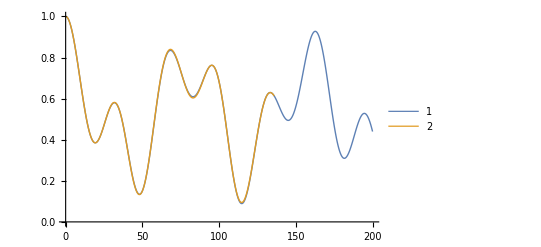

```mathematica
SetDirectory[NotebookDirectory[]];
pp2={0.9998040298691435,0.9992164008629904,0.9982379564554597,0.9968701001566806,0.9951147921089462,0.9929745443503012,0.9904524147813057,0.9875519998770322,0.9842774261756155,0.9806333406233915,0.9766248998097663,0.9722577581777979,0.9675380552744501,0.9624724021185878,0.9570678667661565,0.9513319591559115,0.9452726153189345,0.9388981810369952,0.9322173950346591,0.9252393717869509,0.9179735840352385,0.9104298450706363,0.9026182908788732,0.8945493622109308,0.8862337866478406,0.8776825607215385,0.8689069321452092,0.8599183822153554,0.850728608406725,0.8413495072148731,0.8317931572686131,0.822071802735587,0.8121978370363534,0.802183786875353,0.7920422965903896,0.7817861128157508,0.7714280694481581,0.7609810728974035,0.7504580876027169,0.7398721217823022,0.729236213396612,0.7185634162744016,0.707866786377656,0.6971593681598189,0.6864541809772643,0.6757642055120674,0.6651023701640894,0.6544815373710854,0.6439144898177156,0.6334139164918456,0.6229923985614114,0.6126623950304725,0.6024362281525675,0.5923260685803664,0.5823439202263898,0.5725016048317542,0.5628107462286245,0.5532827543048365,0.543928808671302,0.5347598420484373,0.5257865233934301,0.5170192407953672,0.5084680841735072,0.5001428278206905,0.49205291284058916,0.48420742953396445,0.47661509979521194,0.4692842595861297,0.46222284155905075,0.4554383579060489,0.4489378835154072,0.44272803951689377,0.43681497730745883,0.4312043631387768,0.4259013633609538,0.42091063041015664,0.4162362896268278,0.41188192699251336,0.4078505778689736,0.4041447168196387,0.40076624858994314,0.39771650031728567,0.39499621503621335,0.39260554653669055,0.3905440556276766,0.38881070784984373,0.3874038726713297,0.3863213241962264,0.3855602433992809,0.3851172219018307,0.3849882672824147,0.38516880991540675,0.3856537113180704,0.3864372739781439,0.38751325262536734,0.388874866902027,0.39051481537960114,0.3924252908623801,0.3945979969101085,0.3970241655067921,0.3996945758010157,0.4025995738303,0.4057290931493703,0.4090726762693536,0.4126194968191008,0.41635838233717104,0.4202778376025389,0.42436606841305613,0.4286110057223266,0.43300033004701477,0.43752149606092744,0.4421617572961204,0.4469081908718838,0.4517477221822967,0.45666714947478,0.46165316825881936,0.4666923954897034,0.47177139347815705,0.4768766934834943,0.4819948189508727,0.4871123083673343,0.4922157377070441,0.4972917424494996,0.5023270391571404,0.5073084466045136,0.5122229064560613,0.5170575034939922,0.5217994854016821,0.5264362821114802,0.5309555247287127,0.5353450640457313,0.5395929886631828,0.5436876427332732,0.547617643344208,0.5513718975644312,0.5549396191609948,0.5583103450113399,0.5614739512206264,0.5644206689581519,0.5671411000225982,0.5696262321431971,0.5718674540206109,0.5738565701076053,0.5755858151267238,0.5770478683155251,0.5782358673903172,0.5791434222092495,0.5797646281166337,0.5800940789425983,0.5801268796292433,0.5798586584503133,0.5792855787856781,0.5784043504122817,0.5772122402641863,0.5757070826161654,0.5738872886376418,0.5717518552657548,0.5693003733412517,0.5665330349503102,0.5634506399141344,0.5600546013667682,0.5563469503640549,0.5523303394616754,0.5480080452073955,0.5433839694897137,0.538462639688741,0.5332492075774123,0.5277494469241717,0.5219697497518696,0.515917121211711,0.5095991730353782,0.5030241155341826,0.4962007481185566,0.489138448317802,0.48184715928688626,0.4743373757876233,0.466620128653193,0.45870696773245756,0.45060994333220417,0.4423415861767092,0.4339148859131145,0.42534326819990986,0.4166405704152499,0.40782101604275717,0.39889918778817696,0.3898899994921723,0.38080866691046433,0.37167067743901544,0.3624917588680727,0.3532878472546069,0.3440750540080132,0.33486963228871863,0.3256879428239422,0.31654641924711396,0.3074615330731787,0.298449758422793,0.2895275366095462,0.2807112407072252,0.27201714021415996,0.2634613659287429,0.2550598751564263,0.24682841735749458,0.23878250034958248,0.2309373571732048,0.2233079137253556,0.21590875726207948,0.20875410586606402,0.20185777896998577,0.1952331690204932,0.18889321436143336,0.18285037340864063,0.17711660017942726,0.1717033212386428,0.1666214141049116,0.16188118716765848,0.15749236114341703,0.1534640521016188,0.1498047560803986,0.14652233529822856,0.1436240059792393,0.14111632777665248,0.13900519479382928,0.13729582818464495,0.13599277031323875,0.13509988044648236,0.13462033194776593,0.1345566109362215,0.13491051637160306,0.1356831615216622,0.13687497676605265,0.13848571368856902,0.14051445040780206,0.1429595980951735,0.14581890862865937,0.14908948333038666,0.1527677827365864,0.15684963734914603,0.16133025931910905,0.16620425501394331,0.17146563842210702,0.17710784535044044,0.18312374837246187,0.18950567248570233,0.19624541144379026,0.20333424472419448,0.2107629551012951,0.21852184679279224,0.22660076415116331,0.23498911087351299,0.24367586970492777,0.252649622611969,0.2618985714041361,0.27141055878219966,0.28117308979281547,0.29117335366923525,0.3013982460378709,0.31183439147075714,0.322468166359758,0.33328572209601415,0.344273008525463,0.3554157976580919,0.3666997076034569,0.3781102267034556,0.38963273783112135,0.40125254282178024,0.41295488700039884,0.4247249837663306,0.4365480391940649,0.4484092766059267,0.4602939610706201,0.4721874237776571,0.4840750862372723,0.49594248425295234,0.5077752916101719,0.5195593434254854,0.531280659098602,0.5429254648072527,0.5544802154884738,0.5659316162449238,0.5772666431174398,0.5884725631696975,0.5995369538243075,0.610447721398136,0.6211931187851941,0.6317617622368755,0.6421426471942748,0.652325163130254,0.6622991073633039,0.6720546978097701,0.6815825846459359,0.6908738608566619,0.6999200716527487,0.7087132227449217,0.7172457874676992,0.7255107127544302,0.7335014239668072,0.7412118285922524,0.7486363188259528,0.7557697730616237,0.7626075563196364,0.7691455196451923,0.7753799985180044,0.7813078103159047,0.7869262508805638,0.7922330902369207,0.7972265675211311,0.8019053851735436,0.806268702460755,0.8103161283788334,0.8140477140082423,0.8174639443778225,0.8205657299028025,0.8233543974526981,0.8258316811143925,0.8279997127018452,0.8298610120708473,0.831418477288108,0.8326753747031594,0.8336353289662376,0.8343023130314904,0.8346806381801731,0.8347749440934269,0.8345901889991888,0.8341316399125713,0.8334048629838389,0.8324157139627989,0.8311703287833743,0.8296751142670052,0.8279367389388219,0.8259621239459118,0.8237584340628066,0.8213330687654332,0.8186936533512669,0.8158480300804185,0.8128042493097807,0.8095705605902916,0.806155403695794,0.8025673995509126,0.7988153410248287,0.7949081835578591,0.7908550355882198,0.7866651487474019,0.7823479077940867,0.7779128202584618,0.7733695057712406,0.7687276850544523,0.7639971685542443,0.7591878446994108,0.7543096677731401,0.7493726453894443,0.7443868255699357,0.739362283420934,0.7343091074152929,0.7292373852877844,0.724157189557334,0.7190785626937738,0.7140115019510864,0.7089659438932736,0.7039517486428593,0.698978683885887,0.6940564086706936,0.6891944570405196,0.6844022215452126,0.6796889366741142,0.6750636622615902,0.6705352669143584,0.6661124115098881,0.6618035328202705,0.6576168273132363,0.6535602351834772,0.6496414246670179,0.6458677766908082,0.642246369908764,0.6387839661741396,0.6354869964965151,0.6323615475296782,0.6294133486345348,0.6266477595585607,0.6240697587701589,0.6216839324861155,0.6194944644220367,0.617505126295915,0.6157192691134514,0.6141398152561959,0.6127692513926201,0.6116096222283383,0.6106625251083547,0.6099291054809161,0.6094100532293701,0.6091055998753512,0.6090155166536804,0.6091391134566297,0.6094752386426299,0.6100222797021055,0.6107781647710032,0.6117403649806584,0.6129058976309176,0.6142713301720206,0.615832784979518,0.6175859449054767,0.6195260595885881,0.6216479525050851,0.623946028742196,0.6264142834754567,0.6290463111323389,0.6318353152221562,0.6347741188160526,0.6378551756586807,0.6410705818947672,0.6444120883940754,0.6478711136589314,0.6514387572990761,0.6551058140592098,0.6588627883851003,0.6626999095146363,0.666607147080632,0.6705742272123875,0.6745906491232552,0.6786457021714215,0.6827284833809687,0.6868279154100312,0.6909327649522728,0.6950316615572998,0.6991131168547561,0.7031655441658105,0.7071772784844771,0.7111365968098439,0.7150317388087313,0.7188509277865263,0.7225823919421018,0.726214385880786,0.7297352123571598,0.7331332442173822,0.7363969465084315,0.7395148987194571,0.742475817117792,0.7452685771415518,0.7478822358046633,0.7503060540729425,0.7525295191642545,0.7545423667251178,0.756334602834171,0.7578965257812549,0.759218747569427,0.7602922150859807,0.7611082308875695,0.7616584735437505,0.7619350174828163,0.7619303522835361,0.7616374013565131,0.761049539959254,0.7601606124897003,0.7589649490039327,0.7574573809050449,0.7556332557517711,0.7534884511372735,0.751019387590366,0.7482230404556299,0.7450969507072627,0.7416392346600652,0.7378485925399019,0.7337243158810365,0.729266293720981,0.724475017567243,0.7193515851141628,0.7138977026920168,0.7081156864345866,0.7020084621555397,0.6955795639280694,0.6888331313664328,0.6817739056121022,0.6744072240314434,0.6667390136356947,0.6587757832381339,0.6505246143669708,0.6419931509562882,0.6331895878408396,0.6241226580838758,0.6148016191703235,0.6052362381006273,0.5954367754233136,0.58541396824684,0.575179012273641,0.5647435429014057,0.5541196154382828,0.5433196844805007,0.5323565825022182,0.5212434977085344,0.5099939512035319,0.4986217735259677,0.4871410806056869,0.47556624919422286,0.4639118918230735,0.45219283134322835,0.4404240750992133,0.42862078879063875,0.41679827007388576,0.40497192195574944,0.39315722603044023,0.38136971561043204,0.3696249488009198,0.357938481566788,0.3463258408400489,0.3348024977148588,0.32338384077620547,0.31208514960751554,0.3009215685214215,0.28990808055709893,0.279059481786625,0.2683903559719793,0.25791504961354106,0.24764764742995596,0.23760194830870496,0.22779144176581245,0.21822928495247704,0.2089282802457138,0.19990085345943423,0.1911590327117048,0.18271442798328746,0.17457821140240237,0.16676109828715485,0.15927332898308869,0.1521246515241419,0.14532430514910552,0.13888100470698403,0.1328029259777812,0.12709769193902304,0.12177236000534541,0.1168334102681643,0.11228673475804152,0.10813762775713993,0.10439077718248324,0.10105025705915807,0.0981195211036314,0.09560139743406573,0.09349808442036268,0.091811147689937,0.09054151829833636,0.08968949206717379,0.08925473010294979,0.08923626049746682,0.08963248120398058,0.09044116409189296,0.09165946017272635,0.09328390598751614,0.09531043114481381,0.09773436699407079,0.10055045641599133,0.10375286471041509,0.10733519155621306,0.11129048401692238,0.11561125056216218,0.12028947607213716,0.12531663778978266,0.13068372218249796,0.13638124267289053,0.14239925819568083,0.14872739253566708,0.15535485439967975,0.1622704581736561,0.16946264531435035,0.17691950632379672,0.184628803253475,0.19257799268416922,0.2007542491268,0.20914448878901573,0.2177353936532172,0.22651343580477606,0.23546490196649408,0.24457591817321161,0.2538324745375435,0.2632204500531083,0.2727256373816643,0.28233376757305195,0.2920305346689069,0.3018016201410388,0.3116327171178906,0.3215095543540749,0.3314179198998397,0.3413436844292657,0.3512728241879742,0.36119144352320115,0.37108579696118427,0.3809423107988675,0.3907476041790974,0.40048850962050664,0.4101520929753387,0.41972567279054346,0.4291968390493718,0.4385534712725876,0.4477837559602545,0.45687620335681955,0.46581966352375337,0.47460334170570745,0.4832168129775081,0.4916500361606597,0.49989336699937015,0.5079375705872005,0.5157738330365976,0.5233937723844646,0.5307894487279209,0.5379533735851723,0.5448785184772549,0.5515583227270715,0.5579867004728318,0.5641580468936453,0.5700672436456148,0.5757096635074141,0.5810811742348104,0.5861781416243257,0.5909974317868089,0.595536412632192,0.5997929545675986,0.6037654304115135,0.6074527145275562,0.6108541811822099,0.6139697021317134,0.6167996434442932,0.6193448615648682,0.6216066986304549,0.6235869770456514,0.6252879933286376,0.6267125112395444,0.627863754204191,0.6287453970475828,0.6293615570528907,0.6297167843630536,0.6298160517435096,0.6296647437259898,0.6292686451546109,0.6286339291570286,0.6277671445645723,0.6266752028066406,0.6253653643058429,0.6238452244014514,0.6221226988298472,0.6202060087915041,0.6181036656349038,0.6158244551885054,0.6133774217723983,0.6107718519217258,0.6080172578542274,0.6051233607143901,0.6021000736266178,0.5989574845897272,0.5957058392446029,0.5923555235465056,0.5889170463727302,0.5854010220956518,0.5818181531501775,0.5781792126236448,0.5744950268949894,0.5707764583487978,0.5670343881884798,0.5632796993713428,0.5595232596869256,0.5557759049983911,0.5520484226652244,0.5483515351639102,0.544695883921766,0.5410920133775066,0.5375503552807104,0.5340812132408808,0.5306947475354629,0.527400960184943,0.5242096803020094,0.5211305497206632,0.5181730089103767,0.5153462831795178,0.5126593691717906,0.5101210216588409,0.5077397406319941,0.5055237586959394,0.5034810287672232,0.5016192120806063,0.4999456665067039,0.4984674351849119,0.49719123547621064,0.49612344824132526,0.4952701074506296,0.49463689013322654,0.4942291066738023,0.49405169146708716,0.4941091939410461,0.4944057699612239,0.49494517363009694,0.4957307494965787,0.49676542519217115,0.4980517045115924,0.4995916609568768,0.5013869317651242,0.5034387124410911,0.5057477518167307,0.5083143476605292,0.5111383428600911,0.5142191222018284,0.5175556097718463,0.52114626700206,0.5249890913854636,0.5290816158839404,0.5334209090513852,0.5380035758939843,0.5428257594883521,0.5478831433768764,0.5531709547579313,0.5586839684869259,0.5644165119019627,0.5703624704857063,0.576515294372643,0.5828680057082375,0.5894132068638124,0.5961430895080277,0.6030494445328194,0.6101236728285997,0.6173567969003664,0.6247394733131472,0.6322620059519904,0.6399143600785165,0.6476861771629324,0.6555667904672992,0.6635452413527859,0.6716102962807843,0.6797504644751706,0.6879540162101104,0.6962090016857038,0.7045032704514064,0.7128244913351861,0.7211601728347513,0.7294976839255096,0.7378242752388535,0.7461271005632061,0.7543932386196959,0.7626097150637312,0.7707635246637129,0.7788416536079819,0.7868311018916274,0.7947189057351638,0.8024921599879634,0.8101380404702787,0.8176438262089005,0.8249969215228186,0.8321848779168476,0.8391954157426961,0.8460164455888696,0.8526360893624935,0.859042701028139,0.8652248869706144,0.8711715259506715,0.8768717886244491,0.8823151565994427,0.8874914410015495,0.8923908005295469,0.8970037589749824,0.9013212221870027,0.9053344944630589,0.909035294347654,0.9124157698224288,0.9154685128718109,0.9181865734092035,0.9205634725492903,0.9225932152124703,0.9242703020476613,0.9255897406598395,0.9265470561285926,0.9271383008037761,0.9273600633640596,0.9272094771236762,0.9266842275722244,0.9257825591317406,0.9245032811146663,0.922845772865682,0.9208099880697368,0.9183964582080106,0.9156062951430354,0.9124411928136907,0.908903428020549,0.9049958602817861,0.9007219307399073,0.8960856600997065,0.8910916455782588,0.8857450568483978,0.8800516309580245,0.8740176662087302,0.8676500149786709,0.8609560754763715,0.8539437824141507,0.8466215965922076,0.8389984933870278,0.8310839501406939,0.822887932450894,0.8144208793649099,0.8056936874845858,0.7967176939932605,0.7875046586198339,0.7780667445594946,0.7684164983751661,0.7585668289083685,0.7485309852329238,0.7383225336897009,0.7279553340453779,0.7174435148230178,0.7068014478567285,0.6960437221274849,0.6851851169413874,0.6742405745158853,0.6632251720434,0.6521540933054185,0.6410425999134368,0.6299060022560545,0.618759630234035,0.6076188038673342,0.5964988038595048,0.5854148422063011,0.5743820329357199,0.5634153630669386,0.5525296638750968,0.5417395825479667,0.5310595543190153,0.520503775159298,0.5100861751080543,0.4998203923188207,0.4897197478943126,0.47979722157922267,0.4700654283757699,0.46053659614182213,0.4512225442263353,0.4421346631913652,0.43328389566393677,0.4246807183559131,0.41633512528203304,0.40825661220259074,0.40045416230915043,0.3929362331661223,0.38571074491493984,0.37878506974147264,0.37216602260158616,0.36585985319417325,0.3598722391657627,0.354208280525925,0.34887249524815866,0.34386881602686137,0.33920058815737675,0.3348705685029312,0.3308809255096855,0.32723324022904454,0.3239285083046659,0.320967142880749,0.3183489783875652,0.3160732751602464,0.3141387248473837,0.31254345656703375,0.3112850437690929,0.3103605117650584,0.3097663458883401,0.30949850025095965,0.3095524070654,0.30992298650348477,0.3106046570675357,0.3115913464525083,0.3128765028813799,0.3144531068995958,0.3163136836179141,0.3184503153963908,0.3208546549655389,0.3235179389837035,0.32643100203250763,0.3295842910547272,0.332967880241028,0.3365714863737767,0.34038448463743043,0.3443959249059222,0.3485945485177473,0.3529688055495258,0.35750687259801645,0.3621966710796726,0.3670258860550887,0.3719819855836867,0.37705224061147063,0.3822237453916393,0.387483438434503,0.39281812397939475,0.398214493977074,0.40365915056686774,0.40913862902798936,0.414639421179827,0.42014799920086865,0.42565083983102836,0.4311344489170451,0.4365853862556271,0.4419902906841674,0.44733590536412826,0.45260910319770553,0.4577969123142627,0.46288654155908243,0.4678654059136915,0.4727211517738616,0.4774416820090309,0.48201518072482785,0.4864301376489172,0.49067537206011874,0.4947400561791716,0.4986137379416988,0.5022863630736918,0.5057482963920189,0.5089903422546552,0.5120037640882447,0.5147803029241365,0.5173121948780348,0.5195921875129491,0.5216135550305793,0.5233701122411311,0.5248562272674333,0.5260668329469743,0.526997436899375,0.5276441302356305,0.5280035948914612,0.5280731095740585,0.5278505543177375,0.5273344136528099,0.5265237783959335,0.525418346078729,0.5240184200366975,0.5223249071865669,0.5203393145255542,0.5180637443910634,0.5155008885238352,0.5126540209815488,0.5095269899532613,0.5061242085274297,0.5024506444713762,0.49851180907437553,0.4943137451171753,0.48986301402395044,0.48516668225529846,0.4802323069995808,0.4750679212186021,0.4696820181017074,0.4640835349800665,0.4582818367501526,0.4522866988522875,0.446108289846766,0.4397571536262725};
pp3={0.9998040458190781,0.9992165283517123,0.9982384816702685,0.9968716253959374,0.9951183589856012,0.9929817537968134,0.9904655430416365,0.9875741096634921,0.9843124722970539,0.9806862693965634,0.9767017416935139,0.9723657131251516,0.9676855703962266,0.9626692413418138,0.9573251722669869,0.9516623044392435,0.9456900499118089,0.9394182668526004,0.932857234561582,0.9260176283259728,0.9189104942872725,0.9115472244634893,0.9039395320621516,0.8960994272246348,0.8880391932884014,0.8797713636761699,0.8713086994904384,0.8626641678729297,0.8538509211744845,0.8448822769629571,0.8357716988794665,0.8265327783367725,0.8171792170357658,0.8077248102637339,0.7981834309186794,0.7885690142006913,0.7788955428807006,0.769177033067311,0.7594275203690158,0.7496610463468939,0.7398916451462286,0.7301333301914866,0.720400080826675,0.7107058287831248,0.7010644443613069,0.691489722205976,0.6819953665720999,0.6725949759832327,0.6633020271804805,0.6541298582910235,0.6450916511368884,0.6362004126321247,0.6274689552200947,0.6189098763292459,0.6105355368355355,0.6023580385388172,0.5943892006757459,0.5866405355143423,0.5791232230917285,0.5718480851753989,0.5648255585474733,0.558065667727998,0.551577997270568,0.5453716637819896,0.5394552878264249,0.5338369658971868,0.5285242426446526,0.5235240835580497,0.5188428483107624,0.5144862649826096,0.5104594053722697,0.5067666616267755,0.5034117243881949,0.5003975626815899,0.49772640574434307,0.49539972699104234,0.49341823029669835,0.49178183876874526,0.49048968615513217,0.4895401110249606,0.4889306538297877,0.48865805693875397,0.4887182677079118,0.48910644462908726,0.4898169665689941,0.4908434450877756,0.49217873979868054,0.4938149767028439,0.4957435694119451,0.49795524314086537,0.5004400613339106,0.5031874547609952,0.5061862529088467,0.5094247174627768,0.5128905776731868,0.5165710673695074,0.5204529633949021,0.5245226252107353,0.5287660354274708,0.5331688410037435,0.5377163948703116,0.5423937977322699,0.5471859398104006,0.552077542291494,0.5570531982732044,0.5620974129944315,0.5671946431661363,0.5723293352294196,0.5774859623885507,0.582649060283223,0.5878032611866597,0.5929333266356193,0.5980241784196815,0.603060927874229,0.6080289034426011,0.612913676496821,0.6177010854135295,0.6223772579289922,0.6269286318064458,0.6313419738652883,0.635604397432126,0.6397033782867096,0.6436267691833635,0.6473628130352526,0.6509001548557624,0.6542278525544643,0.6573353866850015,0.6602126692480087,0.6628500516462942,0.6652383318875561,0.6673687611278077,0.6692330496437784,0.6708233723175572,0.6721323737051026,0.6731531727598297,0.6738793672705131,0.6743050380633648,0.674424753016267,0.6742335709118504,0.6737270451627975,0.6729012274239043,0.6717526711011687,0.6702784347573978,0.6684760854128501,0.6663437017264034,0.663879877038741,0.6610837222572841,0.6579548685511316,0.6544934698248502,0.6507002049379551,0.6465762796320625,0.6421234281240957,0.6373439143249318,0.6322405326477457,0.6268166083600928,0.6210759974411985,0.6150230859062538,0.6086627885620117,0.6020005471538049,0.5950423278755497,0.5877946182082857,0.5802644230589857,0.5724592601751766,0.5643871548078441,0.5560566336031657,0.5474767176998546,0.53865691501604,0.529607211703859,0.5203380627587909,0.5108603817668108,0.5011855297714995,0.49132530324768153,0.48129192116459046,0.47109801112299327,0.4607565945476262,0.4502810709213865,0.4396852010409626,0.42898308927615686,0.41818916481699764,0.4073181618895837,0.39638509892684975,0.3854052566748314,0.3743941552262036,0.3633675299716153,0.3523413064609072,0.34133157417393767,0.3303545592064968,0.3194265958836177,0.3085640973147716,0.2977835249281153,0.2871013570097618,0.2765340563049147,0.26609803672873966,0.255809629267346,0.24568504714283412,0.23574035033436144,0.22599140956466535,0.21645386986401602,0.20714311384155248,0.19807422480098524,0.1892619498470406,0.18072066314331026,0.1724643294790788,0.16450646832330648,0.1568601185303024,0.14953780388543253,0.14255149965728173,0.13591260034334057,0.1296318887785556,0.12371950677620239,0.11818492746350936,0.11303692946872235,0.10828357309705187,0.10393217863345312,0.09998930688416299,0.09646074206174413,0.0933514770998289,0.09066570146068922,0.0884067914999232,0.0865773034090255,0.08517896875331378,0.08421269260756607,0.08367855425790868,0.08357581044210954,0.08390290106429478,0.08465745731602156,0.08583631212008855,0.08743551279485286,0.08945033583274106,0.09187530367172493,0.0947042033328899,0.0979301067842489,0.10154539289843573,0.10554177085771482,0.10991030486116898,0.11464143999472065,0.11972502911594807,0.12515036061971235,0.1309061869463035,0.136980753706957,0.1433618293038927,0.15003673492640388,0.15699237482304484,0.1642152667485409,0.17169157249883826,0.1794071284549935,0.18734747606743732,0.195497892222474,0.203843419438957,0.21236889585407276,0.22105898496723386,0.22989820511094144,0.23887095864116734,0.24796156082773924,0.2571542684408086,0.26643330803281373,0.27578290391929733,0.28518730586384644,0.2946308164734096,0.30409781831396726,0.3135728007543877,0.32304038654612804,0.33248535814433594,0.34189268377321264,0.3512475432359877,0.36053535346349425,0.3697417937931229,0.37885283096166045,0.38785474379459395,0.39673414755846975,0.40547801795162,0.4140737146846763,0.42250900460795193,0.4307720843318093,0.4388516022788935,0.44673668010265577,0.45441693339989725,0.4618824916405367,0.46912401723192104,0.4761327236331131,0.4829003924329805,0.4894193892981691,0.4956826787034177,0.5016838373523362,0.5074170661997699,0.51287720099073,0.5180597212319998,0.5229607575204447,0.5275770971575227,0.5319061879855785,0.5359461403920495,0.5396957274375894,0.5431543830727833,0.5463221984215851,0.5491999161207473,0.551788922718655,0.554091239148382,0.556109509304319,0.5578469867660091,0.5593075197255428,0.560495534188995,0.5614160155339404,0.5620744885185885,0.5624769958503929,0.5626300754304884,0.56254073640421,0.562216434148535,0.5616650443444801,0.5608948362810735,0.5599144455433941,0.5587328462418698,0.5573593229390763,0.5558034424304317,0.5540750255336055,0.5521841190367925,0.5501409679507079,0.5479559882039132,0.5456397399119262,0.543202901340618,0.5406562436734295,0.5380106066852075,0.5352768754024124,0.532465957829271,0.5295887637959376,0.5266561849748118,0.5236790760953641,0.5206682373752183,0.5176343981694046,0.5145882018251638,0.511540191721734,0.5085007984510814,0.5054803280967259,0.502488951547346,0.4995366947759403,0.49663343000585514,0.49378886767798696,0.491012549125642,0.48831383986253907,0.4857019233829006,0.4831857953699092,0.48077425821251,0.47847591572886744,0.47629916799659294,0.47425220619524083,0.47234300737067925,0.4705793290372982,0.4689687035416361,0.4675184321184467,0.46623557857985504,0.46512696258838965,0.46419915247512844,0.463458457573811,0.46291092005431,0.4625623062513602,0.4624180974926041,0.46248348044436505,0.4627633370033353,0.46326223377444664,0.4639844111829433,0.46493377228035815,0.4661138713134586,0.4675279021303893,0.46917868650755234,0.4710686624874981,0.4731998728211654,0.4755739536116811,0.47819212326241,0.4810551718294556,0.48416345088198076,0.48751686397211935,0.4911148578122296,0.4949564142578851,0.49904004318807976,0.5033637763675517,0.5079251623728754,0.5127212626551303,0.5177486488042536,0.5230034010720254,0.5284811082002521,0.5341768685943472,0.5400852928684753,0.546200507782018,0.552516161575377,0.5590254307038459,0.565721027958607,0.5725952119544548,0.5796397979554679,0.5868461700002474,0.594205294282479,0.6017077337338483,0.6093436637510257,0.6171028890025875,0.6249748612467775,0.6329486980902069,0.6410132026068336,0.6491568837448842,0.6573679774406639,0.6656344683604114,0.6739441121911022,0.6822844584044404,0.6906428734142706,0.6990065640570469,0.7073626013229408,0.7156979442698947,0.7239994640573983,0.7322539680386848,0.7404482238547963,0.7485689834828152,0.7566030071832004,0.7645370873098187,0.7723580719402542,0.7800528882919354,0.7876085658928286,0.7950122594790664,0.8022512715951319,0.8093130748746389,0.8161853339851975,0.8228559272186231,0.8293129677106287,0.8355448242805807,0.8415401418767711,0.8472878616162658,0.8527772404077609,0.857997870148631,0.8629396964798496,0.867593037090766,0.8719485995605092,0.8759974987176266,0.8797312735059145,0.883141903336701,0.8862218239115461,0.8889639424891896,0.8913616525776478,0.8934088480258382,0.8950999364877407,0.8964298522302935,0.897394068256702,0.8979886077112645,0.8982100545344187,0.8980555633319263,0.8975228684257829,0.8966102920492766,0.8953167516521254,0.8936417662779753,0.8915854619784391,0.8891485762308473,0.8863324613243536,0.8831390866809261,0.8795710400873622,0.8756315277971704,0.8713243734880556,0.866654016046893,0.861625506163058,0.8562445017137444,0.8505172619286734,0.8444506403255291,0.8380520764113099,0.8313295861505924,0.824291751203459,0.8169477069418383,0.8093071292583988,0.8013802201846588,0.7931776923401311,0.7847107522375119,0.7759910824776174,0.7670308228597402,0.7578425504513555,0.7484392586538743,0.7388343353074667,0.7290415398799566,0.7190749797869121,0.7089490858916861,0.6986785872352842,0.6882784850487809,0.6777640260972689,0.6671506754108432,0.6564540884537158,0.6456900827848955,0.6348746092626314,0.624023722845108,0.6131535530400033,0.6022802740546473,0.5914200746984487,0.5805891280888171,0.5698035612124356,0.5590794243932127,0.5484326607186604,0.53787907547721,0.5274343056579222,0.5171137895691346,0.5069327366280051,0.49690609737843305,0.4870485337945316,0.4773743899289463,0.4678976629657204,0.45863197474224005,0.4495905438025629,0.4407861580491915,0.4322311480606128,0.42393736114388103,0.4159161361925642,0.408178279421488,0.40073404105034277,0.39359309300922823,0.38676450773403054,0.3802567381317896,0.37407759877661184,0.3682342484110802,0.36273317381642256,0.3575801751149804,0.3527803525652524,0.3483380949044236,0.34425706928934297,0.34054021288146996,0.33718972611564946,0.33420706768628183,0.33159295127797683,0.329347344060697,0.32746946696223656,0.3259577967239471,0.3248100697353809,0.32402328764212385,0.3235937247057438,0.32351693689224315,0.3237877726571319,0.32440038538722804,0.3253482474532483,0.3266241658205258,0.3282202991593317,0.33012817639067327,0.3323387165986207,0.33484225023564,0.3376285415437636,0.340686812111361,0.3440057654820007,0.34757361273155624,0.35137809892747673,0.35540653038315784,0.3596458026215912,0.364082428962545,0.36870256964907355,0.3734920614300257,0.3784364475201102,0.38352100785848403,0.3887307895925502,0.39405063771610027,0.39946522579510124,0.40495908671832637,0.41051664341408917,0.41612223947859367,0.42176016966608965,0.427414710193895,0.43307014882117084,0.4387108146626077,0.4443211077023417,0.44988552797663706,0.4553887043966129,0.4608154231848465,0.46615065590135163,0.4713795870369042,0.47648764115112435,0.48146050953539243,0.486284176378852,0.4909449444166057,0.4954294600379945,0.49972473783166815,0.5038181845426375,0.5076976224149663,0.5113513118892725,0.5147679736269986,0.5179368098256123,0.5208475247881151,0.5234903447088307,0.5258560366336904,0.5279359265515162,0.5297219165700074,0.531206501129163,0.5323827822031594,0.5332444834393053,0.5337859631858165,0.5340022263552615,0.5338889350748718,0.5334424180743662,0.5326596787640617,0.5315384019583522,0.5300769592026672,0.5282744126656052,0.5261305175618383,0.5236457230769302,0.520821171769271,0.5176586974308959,0.5141608213950285,0.510330747283942,0.5061723541980897,0.5016901883542533,0.49688945318750816,0.4917759979385808,0.4863563047555033,0.48063747434545645,0.4746272102191667,0.46833380157695487,0.4617661048915812,0.4549335242490461,0.4478459905127017,0.44051393938311434,0.4329482884285684,0.42516041316458997,0.41716212226551497,0.40896563199250746,0.40058353992421053,0.39202879807970215,0.383314685518211,0.37445478050813397,0.36546293235069394,0.3563532329453523,0.34713998818181896,0.33783768924112245,0.32846098388562267,0.3190246478146963,0.30954355615939033,0.3000326551854482,0.29050693427027885,0.28098139821419954,0.27147103994387634,0.26199081365913396,0.2525556084708347,0.24318022257271926,0.2338793379854986,0.2246674959069498,0.21555907269734725,0.2065682565254674,0.1977090246962198,0.1889951216772877,0.1804400378385381,0.17205698891505067,0.16385889619999944,0.15585836747350743,0.14806767867071863,0.14049875628732908,0.1331631605227893,0.12607206915824104,0.11923626216549237,0.11266610704253067,0.10637154487070563,0.10036207708838371,0.09464675297602557,0.0892341578493683,0.08413240194947087,0.07934911003851342,0.07489141168797535,0.07076593226132753,0.0669787845895055,0.06353556133780852,0.06044132807127385,0.0577006170154548,0.05531742151759407,0.05329519121084326,0.05163682789234928,0.05034468211578635,0.04942055050848646,0.04886567381699979,0.04868073569516802,0.04886586223547363,0.04942062225682358,0.0503440283538447,0.05163453871587361,0.053290059722329225,0.055307949321612024,0.05768502119320519,0.06041754970612764,0.0635012756691577,0.06693141287600707,0.07070265544624174,0.07480918595551053,0.0792446843597035,0.08400233769924506,0.08907485057997189,0.09445445642051142,0.10013292945489542,0.10610159747799647,0.11235135531503723,0.11887267900653331,0.12565564068047647,0.13268992409472885,0.13996484083598207,0.14746934713928467,0.15519206131086688,0.16312128172689888,0.17124500538134216,0.17955094695398877,0.18802655837122456,0.19665904882975865,0.2054354052492514,0.21434241313039337,0.22336667778002275,0.23249464587494473,0.24171262733177795,0.25100681745065095,0.2603633193002748,0.2697681663122744,0.27920734505090816,0.28866681812684386,0.2981325472226527,0.3075905161956732,0.31702675422650195,0.3264273589800509,0.33577851974627315,0.34506654052750685,0.3542778630392668,0.3633990895917406,0.3724170058147036,0.3813186031995523,0.3900911014163616,0.3987219703753874,0.4071989519975488,0.4155100816565951,0.42364370926046413,0.4315885199319036,0.43933355425334136,0.44686822803808957,0.45418235159017106,0.4612661484145465,0.46811027333920224,0.4747058300101565,0.48104438772151425,0.48711799754003976,0.4929192076864862,0.49844107813542493,0.5036771943951364,0.5086216804303544,0.5132692106913864,0.5176150212141376,0.52165491975693,0.5253852949413269,0.5288031243659215,0.5319059816642725,0.5346920424797277,0.5371600893326781,0.5393095153581784,0.5411403268948196,0.5426531449073325,0.5438492052319397,0.5447303576318239,0.5452990636574357,0.5455583933079352,0.5455120204940582,0.5451642173062914,0.5445198470956302,0.5435843563781759,0.5423637655781479,0.5408646586273131,0.5390941714422749,0.5370599793055466,0.5347702831760732,0.5322337949623528,0.5294597217906529,0.5264577493049537,0.5232380240353558,0.5198111348787422,0.516188093729977,0.512380315309152,0.5083995962289702,0.5042580933474192,0.49996830145252447,0.4955430303234845,0.49099538121596353,0.4863387228205751,0.481586666732662,0.4767530424815989,0.471851872170269,0.4668973447591722,0.46190379004134485,0.45688565234922324,0.45185746403389726,0.4468338187551108,0.44182934462083806,0.4368586772132552,0.4319364325373918,0.42707717992779476,0.42229541494853723,0.4176055323203198,0.4130217989092025,0.40855832681078674,0.40422904656390424,0.4000476805281545,0.396027716460125,0.39218238132371286,0.3885246153709374,0.3850670465305403,0.381821965142881,0.3788012990808769,0.37601658929822834,0.37347896584798046,0.37119912441346564,0.3691873034015577,0.3674532616413562,0.3660062567388582,0.36485502413779053,0.36400775693746873,0.363472086520409,0.3632550640430514,0.3633631428436692,0.36380216182198977,0.3645773298452518,0.3656932112351652,0.3671537123900652,0.3689620695947196,0.3711208380703038,0.37363188231496935,0.37649636778355994,0.3797147539511287,0.3832867888043766,0.38721150480059746,0.39148721633035377,0.39611151871607014,0.40108128877534605,0.40639268696849706,0.4120411611553071,0.4180214519684148,0.4243275998126388,0.4309529534922917,0.43789018046237127,0.4451312786936046,0.45266759013527375,0.4604898157537842,0.4685880321188516,0.4769517095025799,0.48556973145225035,0.4944304157906269,0.5035215369913166,0.5128303498740299,0.52234361455731,0.5320476226016265,0.5419282242725212,0.5519708568486414,0.5621605738961108,0.5724820754274044,0.5829197388602422,0.593457650689379,0.6040796387838276,0.6147693052174346,0.6255100595437767,0.6362851524232309,0.6470777095111254,0.6578707655161766,0.6686472983393287,0.6793902632044564,0.6900826266940111,0.7007074006048087,0.7112476755414852,0.721686654167813,0.7320076840389514,0.7421942899409535,0.7522302056670318,0.7620994051636798,0.7717861329833372,0.781274933983953,0.790550682219593,0.799598608969993,0.8084043298603933,0.8169538710287266,0.8252336942964933,0.8332307213082856,0.8409323566055396,0.8483265096042105,0.8554016154492924,0.8621466547222915,0.8685511719802291,0.8746052931103758,0.8802997414805261,0.8856258528760539,0.8905755892123565,0.8951415510124369,0.8993169886433825,0.9030958123082883,0.9064726007893682,0.9094426089408552,0.9120017739314235,0.9141467202371473,0.9158747633871371,0.9171839124645957,0.9180728713683555,0.9185410388429036,0.9185885072727098,0.918216060259853,0.9174251689862722,0.9162179873704676,0.9145973460281513,0.912566745047031,0.9101303455883025,0.9072929603248974,0.9040600427325305,0.9004376752471731,0.8964325563054183,0.8920519862854299,0.8873038523678081,0.8821966123370583,0.8767392773480693,0.8709413936806872,0.8648130235099258,0.8583647247218842,0.8516075298084743,0.8445529238728037,0.8372128217825858,0.8295995445136757,0.8217257947244915,0.8136046316073015,0.8052494450647113,0.796673929262672,0.7878920556141509,0.77891804525029,0.7697663410388791,0.7604515792141009,0.7509885606779395,0.7413922220452576,0.7316776064994907,0.7218598345305126,0.7119540746269937,0.7019755139984455,0.6919393294007815,0.6818606581419469,0.6717545693433531,0.6616360355326332,0.651519904645809,0.6414208725080685,0.631353455871778,0.6213319660804363,0.6113704834285456,0.6014828322840241,0.5916825570369595,0.5819828989349187,0.5723967738614967,0.5629367511103841,0.5536150332030828,0.5444434367929074,0.5354333746955084,0.5265958390747445,0.5179413858156421,0.509480120103984,0.501221683229248,0.49317524062127566,0.48534947112530075};
pp4={0.9998040617723246,0.999216655835854,0.9982390066839468,0.9968731493437465,0.9951219207474666,0.9929889477926549,0.9904786322506038,0.9875961326489759,0.9843473433577857,0.9807388711028423,0.9767780091604911,0.9724727095069561,0.9678315532135071,0.9628637193931493,0.9575789530039719,0.9519875318196588,0.9461002328737116,0.939928298675343,0.933483403495018,0.9267776199682144,0.9198233862837303,0.9126334741974087,0.9052209580422856,0.8975991849318659,0.889781746286117,0.8817824507999913,0.8736152989285519,0.8652944589350233,0.856834244514558,0.8482490939735822,0.8395535509126248,0.8307622463428711,0.8218898821061908,0.8129512154901427,0.8039610448690736,0.7949341961970572,0.7858855101602576,0.7768298297817996,0.7677819882620088,0.7587567968263997,0.7497690323732403,0.7408334246560383,0.7319646428150863,0.7231772810218557,0.7144858430347985,0.7059047254813244,0.6974481996889197,0.6891303919126887,0.680965261831844,0.6729665792163386,0.6651478986851904,0.6575225325234748,0.6501035215495864,0.6429036040500307,0.6359351828555968,0.6292102906562894,0.6227405536871367,0.6165371539645027,0.6106107902813107,0.6049716382030332,0.5996293093456049,0.5945928102407837,0.5898705011272325,0.5854700550271744,0.5813984174908848,0.577661767405202,0.5742654792751936,0.5712140873926299,0.5685112523103398,0.5661597300332505,0.5641613443244203,0.5625169625127034,0.5612264751639532,0.5602887799503212,0.5597017700181425,0.559462327109006,0.5595663196689571,0.5600086061012095,0.5607830432877879,0.5618825004452115,0.5632988783242734,0.5650231337030379,0.5670453090684716,0.5693545673209444,0.5719392312865497,0.5747868277583194,0.577884135749744,0.5812172385832721,0.5847715794129335,0.5885320197314986,0.5924829003837118,0.596608104595649,0.6008911225040326,0.6053151166629892,0.6098629880112928,0.6145174417769818,0.6192610528215532,0.6240763299341725,0.6289457786212376,0.6338519619593541,0.6387775591208666,0.6437054212187794,0.6486186241605651,0.653500518246327,0.6583347742975973,0.6631054261404958,0.6677969093334095,0.6723940960596885,0.676882326158972,0.6812474343207406,0.6854757734931127,0.6895542346086093,0.6934702627580175,0.6972118699769662,0.7007676448298984,0.704126759005476,0.7072789711465478,0.7102146281601821,0.7129246642458238,0.7154005978982797,0.7176345271325116,0.7196191231723781,0.721347622847226,0.7228138199076243,0.7240120554843024,0.7249372078788598,0.7255846818640885,0.725950397653845,0.7260307796804502,0.7258227452969634,0.7253236935037384,0.7245314937787771,0.7234444750696224,0.7220614149916531,0.7203815292499974,0.7184044613092445,0.7161302722967426,0.7135594311224931,0.7106928048008067,0.7075316489365084,0.7040775983379548,0.7003326577222234,0.6962991924578525,0.6919799193182371,0.6873778972023495,0.6824965177884131,0.6773394960955265,0.6719108609339859,0.6662149452368427,0.6602563762711525,0.6540400657428423,0.6475711998152949,0.6408552290809137,0.633897858529624,0.626705037570309,0.61928295017482,0.6116380052214396,0.603776827119144,0.5957062468013706,0.5874332931858819,0.578965185192057,0.5703093244094535,0.5614732885104933,0.5524648254894595,0.543291848799328,0.5339624334553696,0.5244848131526019,0.5148673784280183,0.5051186758850467,0.4952474084682559,0.48526243676244074,0.47517278125877965,0.4649876255119366,0.45471632007813423,0.44436838710812576,0.4339535254385341,0.4234816159991436,0.4129627273359314,0.40240712102468124,0.39182525673995033,0.3812277967197067,0.3706256093627371,0.36002977168549066,0.34945157037119945,0.3389025011316601,0.3283942661279484,0.3179387691963321,0.30754810864968546,0.2972345674483676,0.2870106005583949,0.2768888193542157,0.266881972951527,0.25700292640639943,0.24726463574921873,0.23768011987530985,0.22826242935521365,0.2190246122816007,0.20997967730922001,0.2011405540980975,0.19252005140884088,0.18413081314348104,0.1759852726623688,0.1680956057403653,0.1604736825560879,0.15313101912910934,0.1460787286429583,0.139327473093666,0.1328874157171178,0.12676817463889137,0.12097877819094385,0.11552762231435804,0.11042243045718717,0.10567021633364464,0.10127724990063466,0.09724902685694309,0.09359024191788283,0.09030476611544694,0.0873956282763534,0.0848650008173691,0.08271418993943745,0.08094363024339239,0.07955288375898945,0.0785406433118079,0.0779047401279402,0.07764215551935055,0.07774903646204126,0.07822071483712305,0.07905173008608338,0.08023585499465477,0.08176612430113515,0.08363486581413936,0.08583373370060493,0.08835374361676873,0.09118530933542399,0.09431828053817676,0.0977419814343558,0.10144524989598248,0.1054164767969828,0.10964364527890877,0.11411436966445401,0.11881593378202979,0.12373532848671201,0.12885928816883624,0.13417432610154398,0.13966676848564086,0.14532278707083232,0.15112843029220985,0.157069652847598,0.1631323437094448,0.16930235255775353,0.17556551466333004,0.18190767427081095,0.18831470654636862,0.19477253817841178,0.20126716674005446,0.20778467892493852,0.2143112677986226,0.22083324919666059,0.2273370774189335,0.2338093603759165,0.2402368743364262,0.2466065784307151,0.25290562905844605,0.2591213943408606,0.2652414687528478,0.2712536880573848,0.2771461446484342,0.28290720340260744,0.28852551811366783,0.2939900485666683,0.2992900782957131,0.30441523304171797,0.30935549990587075,0.3141012471779108,0.3186432447900108,0.3229726853299282,0.32708120552261744,0.33096090807081013,0.33460438372981055,0.3380047334645623,0.34115559053062106,0.34405114230329586,0.34668615166558847,0.34905597775952124,0.3511565959016135,0.35298461645215184,0.35453730243051074,0.35581258567712326,0.35680908135988965,0.35752610063268,0.35796366126642143,0.35812249608803104,0.3580040590701661,0.35761052894585005,0.35694481023044833,0.3560105315626604,0.3548120412968089,0.35335440030065535,0.35164337194566575,0.3496854092919828,0.34748763950346523,0.3450578455513251,0.34240444528914843,0.33953646800321363,0.3364635285685269,0.33319579935826854,0.3297439800760884,0.3261192656927818,0.32233331268697174,0.31839820380720313,0.3143264115668346,0.31013076070483747,0.3058243898441846,0.3014207125803429,0.296933378233607,0.292376232497875,0.28776327820523084,0.28310863642621353,0.27842650810874053,0.27373113644792313,0.2690367701700392,0.26435762788894007,0.2597078636819001,0.25510153401326235,0.2505525661130903,0.2460747278976784,0.2416815994990924,0.23738654644708845,0.2332026945390241,0.2291429063899173,0.2252197596583334,0.221445526909131,0.21783215706547635,0.2143912583823468,0.21113408286005564,0.20807151200196194,0.20521404381143765,0.20257178091261122,0.20015441967395572,0.1979712402097653,0.19603109712883926,0.1943424109050218,0.19291315974383774,0.1917508718262601,0.19086261781618621,0.1902550035308698,0.18993416267425334,0.18990574957275036,0.19017493183262338,0.19074638288233503,0.19162427436868992,0.19281226839315294,0.1943135095985325,0.1961306171312171,0.19826567652519023,0.20072023156852759,0.20349527623056562,0.20659124675094895,0.2100080139938202,0.21374487619260452,0.2178005522186493,0.22217317551022894,0.2268602888087794,0.23185883985302583,0.2371651781749737,0.24277505314770148,0.24868361341994644,0.2548854078712763,0.26137438820695896,0.268143913300459,0.27518675537169635,0.2824951080811702,0.29006059658692473,0.29787428960266116,0.3059267134700785,0.31420786823548486,0.3227072456990445,0.3314138493866321,0.34031621636888126,0.3494024408358214,0.3586601993157529,0.36807677740848177,0.3776390978942771,0.3873337500598839,0.39714702007951647,0.4070649222809055,0.41707323111793926,0.42715751367507065,0.43730316252744705,0.44749542878498566,0.45771945515768525,0.4679603088828519,0.47820301437374035,0.4884325854550782,0.498634057069728,0.5087925163561193,0.5188931330110207,0.5289211888711318,0.5388621066636391,0.5487014778921732,0.5584250898417276,0.5680189517028525,0.5774693198235985,0.586762722118581,0.5958859816679319,0.6048262395488849,0.6135709769520422,0.6221080366334092,0.6304256437577291,0.6385124261864283,0.6463574342604065,0.6539501601197306,0.661280556598911,0.6683390557225982,0.6751165868180009,0.6816045942440607,0.6877950547279081,0.6936804942803966,0.6992540046494461,0.7045092592561885,0.709440528539229,0.714042694623303,0.7183112652123647,0.7222423865972518,0.7258328556549579,0.7290801307095427,0.7319823411188868,0.7345382954463323,0.7367474880777569,0.7386101041361284,0.7401270225637275,0.7412998172344868,0.7421307559768768,0.7426227973953567,0.7427795853931897,0.7426054413164305,0.7421053536572068,0.7412849652712197,0.7401505580934626,0.7387090353556678,0.7369679013350738,0.7349352386803455,0.7326196834040142,0.7300303976415923,0.7271770403096399,0.7240697358139604,0.7207190409922313,0.7171359104828741,0.7133316607473589,0.7093179329788695,0.7051066551526224,0.7007100034790217,0.6961403635379227,0.6914102913699067,0.6865324748096653,0.6815196953410532,0.6763847907506879,0.6711406188495109,0.6658000225154347,0.6603757963006613,0.6548806548241477,0.6493272031504523,0.6437279093292502,0.6380950792430786,0.6324408338868359,0.6267770891582826,0.6211155382245589,0.6154676364792567,0.6098445890829869,0.6042573410401197,0.598716569735943,0.593232679823463,0.5878158003213338,0.5824757837558658,0.5772222071547172,0.5720643746780579,0.5670113216535309,0.5620718197658701,0.5572543831417255,0.552567275060699,0.5480185150229799,0.5436158859018843,0.5393669409178128,0.5352790101769694,0.5313592065306466,0.5276144305317952,0.5240513742806303,0.5206765239778698,0.5174961610289894,0.5145163615706193,0.5117429943197316,0.5091817166805696,0.5068379690702778,0.5047169674633585,0.5028236941820152,0.5011628869929124,0.49973902659829433,0.4985563226407729,0.49761869836511885,0.4969297741036365,0.49649284977321173,0.4963108865898613,0.4963864882190133,0.4967218815923413,0.49731889762826686,0.4981789520972908,0.4993030268726727,0.5006916518039892,0.5023448874467586,0.504262308863868,0.5064429907129796,0.5088854938105006,0.5115878533476803,0.5145475689157685,0.5177615964751533,0.5212263423819697,0.5249376595611143,0.5288908458939693,0.5330806448605003,0.5375012484586232,0.5421463023953175,0.5470089135228323,0.5520816594763196,0.557356600446242,0.5628252930007938,0.5684788058599114,0.5743077375068816,0.5803022355117043,0.5864520174306544,0.5927463931375894,0.5991742884403924,0.6057242698263261,0.6123845701841792,0.6191431153501699,0.6259875513246654,0.6329052720123363,0.6398834473461468,0.6469090516594718,0.6539688921818174,0.6610496375391923,0.6681378461550782,0.6752199944566556,0.682282504801739,0.6893117730551173,0.6962941957545087,0.7032161968156483,0.7100642537409997,0.716824923305397,0.7234848667005681,0.7300308741325006,0.7364498888721995,0.7427290307679298,0.7488556192331215,0.7548171957293905,0.7606015457647507,0.7661967204332794,0.771591057520915,0.7767732022012976,0.7817321273438336,0.7864571534544124,0.7909379682629799,0.7951646459660215,0.7991276661299102,0.802817932249713,0.8062267899529604,0.8093460448290751,0.8121679798560085,0.8146853723864467,0.8168915106518709,0.818780209730231,0.8203458269175852,0.8215832764379067,0.8224880434134112,0.823056197021695,0.8232844027585973,0.8231699337147124,0.8227106807865125,0.8219051617321576,0.8207525289858567,0.8192525761488331,0.8174057430780957,0.8152131195019586,0.8126764470897224,0.8097981199236352,0.806581183317856,0.803029330947639,0.7991469002580007,0.7949388661362116,0.7904108328384208,0.7855690241789418,0.7804202720022957,0.7749720029651725,0.7692322236718773,0.7632095042190014,0.7569129602128061,0.7503522333355489,0.7435374705439327,0.7364793019944336,0.7291888177945413,0.721677543686401,0.713957415773139,0.7060407544054962,0.6979402373395107,0.689668872287684,0.6812399689783994,0.6726671108400009,0.6639641264200118,0.655145060646817,0.6462241460395731,0.6372157739591848,0.6281344659917079,0.6189948455438343,0.6098116097270947,0.6005995015900677,0.591373282755064,0.5821477065066689,0.5729374913665455,0.563757295180848,0.5546216897390327,0.5455451359316555,0.536541959449756,0.5276263270180437,0.5188122231493699,0.5101134274004083,0.5015434921064494,0.4931157205658659,0.48484314564520387,0.4767385087710627,0.46881423927829813,0.461082434082105,0.4535548376441848,0.4462428222049895,0.43915736826322027,0.43230904528181463,0.4257079926111252,0.4193639006256061,0.4132859920781057,0.4074830036839806,0.40196316795780596,0.3967341953321223,0.3918032566015625,0.3871769657412878,0.38286136315944763,0.37886189945507087,0.3751834197559447,0.37183014872516656,0.368805676330905,0.3661129444704299,0.36375423456275313,0.36173115621420493,0.36004463706353906,0.35869491392172415,0.35768152531307196,0.3570033055304167,0.35665838030367014,0.3566441641813156,0.35695735971694503,0.35759395854021975,0.358549244388224,0.3598177981541666,0.3613935050032623,0.36326956358838597,0.36543849738712453,0.3678921681614941,0.37062179153354047,0.373617954645718,0.37687063586619285,0.3803692264765689,0.3841025542751667,0.3880589090042115,0.39222606949844546,0.39659133244697975,0.40114154263845825,0.40586312455985635,0.41074211520681264,0.4157641979553827,0.42091473734471785,0.42617881461441265,0.43154126384138164,0.4369867085217624,0.44249959844400116,0.44806424670613954,0.4536648667356675,0.45928560917585676,0.46491059851412697,0.47052396933567686,0.4761099020961397,0.4816526583189462,0.4871366151364984,0.4925462991008044,0.49786641920840685,0.5030818990910312,0.5081779083366142,0.5131398929166042,0.5179536047023229,0.5226051300689465,0.5270809175845672,0.5313678047946642,0.5354530441164299,0.5393243278591406,0.542969812391162,0.5463781414740535,0.5495384687839993,0.5524404796385866,0.5550744119432377,0.5574310763669746,0.559501875754262,0.5612788237646025,0.5627545627349728,0.5639223807433893,0.5647762278462575,0.5653107314528875,0.5655212107900882,0.5654036904057226,0.5649549126389439,0.5641723489936671,0.5630542103312245,0.5615994557975503,0.5598078003938737,0.5576797210950154,0.5552164614191631,0.5524200343500216,0.5492932235140177,0.5458395825176471,0.5420634323544625,0.537969856796381,0.5335646956951946,0.5288545361245522,0.5238467013078255,0.5185492372871876,0.5129708973103754,0.5071211239151523,0.5010100287172087,0.4946483699207815,0.48804752758919123,0.48121947673044707,0.4741767582708749,0.46693244800832046,0.45950012365250825,0.4518938300775909,0.44412804292741204,0.43621763072887154,0.42817781567914304,0.4200241332909299,0.41177239108058084,0.4034386264979685,0.39503906430167307,0.3865900735863336,0.3781081246670057,0.36960974603486374,0.3611114815843234,0.35262984831309235,0.344181294689459,0.335782159870741,0.3274486339475974,0.3191967193757501,0.31104219374456665,0.3030005740154948,0.2950870823493126,0.28731661362166855,0.2797037047146011,0.27226250565065885,0.2650067526174308,0.25794974291667344,0.2511043118597705,0.2444828116027992,0.23809709191187955,0.23195848282986697,0.2260777792039867,0.2204652270226885,0.21513051150002596,0.21008274683938338,0.2053304675973975,0.20088162156810618,0.1967435641022323,0.19292305377483637,0.18942624930986476,0.1862587076804796,0.18342538329878447,0.18093062820936284,0.17877819321467464,0.17697122985896885,0.17551229320307823,0.17440334533234353,0.17364575954560915,0.17324032517910568,0.17318725302804439,0.17348618133364846,0.17413618231268796,0.17513576921267293,0.17648290388100657,0.17817500484320814,0.18020895588907873,0.1825811151695562,0.18528732481685595,0.1883229210903051,0.19168274506560662,0.19536115387714897,0.1993520325275594,0.20364880627654947,0.20824445361977778,0.21313151986744966,0.21830213132733217,0.22374801009622056,0.2294604894560498,0.23543052987415253,0.2416487355922916,0.248105371795728,0.2547903823323073,0.26169340797246377,0.2688038051677687,0.27611066527908845,0.2836028342355963,0.2912689325818657,0.29909737586669316,0.30707639532483977,0.3151940587980862,0.32343829184333217,0.33179689897125847,0.3402575849571012,0.3488079761709634,0.3574356418681933,0.3661281153852911,0.3748729151882354,0.38365756572254267,0.3924696180153917,0.40129666998608776,0.4101263864219083,0.41894651858349025,0.42774492340435877,0.43650958225928216,0.44522861927077156,0.4538903191408866,0.4624831444909004,0.47099575269235566,0.47941701218847,0.48773601829898133,0.4959421085092582,0.5040248772445165,0.5119741901350922,0.5197801977785775,0.5274333490064713,0.5349244036644161,0.5422444449127901,0.5493848910593513,0.5563375069258574,0.5630944147594522,0.5696481046898052,0.575991444735221,0.5821176903564005,0.5880204935546446,0.5936939115066898,0.5991324147276593,0.6043308947493471,0.6092846712971854,0.6139894989469007,0.6184415732394799,0.622637536230877,0.6265744814496969,0.6302499582320558,0.6336619754084676,0.636809004309627,0.6396899810615144,0.6423043081379549,0.6446518551447333,0.6467329588033209,0.6485484221087825,0.6500995126415169,0.6513879600089725,0.6524159524039559,0.6531861322631466,0.6537015910215973,0.6539658629585918,0.6539829181354578,0.6537571544351541,0.6532933887139079,0.6525968470865388,0.6516731543654372,0.650528322684791,0.6491687393425911,0.6476011539023286,0.6458326645945108,0.6438707040694338,0.6417230245519064,0.6393976824498345,0.6369030224795849,0.6342476613639019,0.6314404711682196,0.6284905623297727,0.6254072664500737,0.6222001189100342,0.6188788413659799,0.6154533241890459,0.6119336089054568,0.6083298706868705,0.6046524009460209,0.600911590082294,0.5971179104184445,0.59328189936452,0.5894141428419918,0.5855252589924195,0.5816258821911208,0.5777266473776329,0.5738381747128943,0.5699710545610694,0.566135832792791,0.5623429964000101,0.5586029594028983,0.554926049026976,0.5513224921267184,0.5478024018205687,0.5443757643044363,0.5410524258047821,0.5378420796308475,0.5347542532840855,0.5317982955819257,0.5289833637537685,0.5263184104680522,0.5238121707509644,0.521473148761223,0.5193096043889558,0.5173295396518428,0.5155406848670945,0.5139504845861057,0.5125660832820854,0.511394310794158,0.5104416675358878,0.5097143094864311,0.5092180329925977,0.5089582594171166,0.5089400196796651,0.5091679387462322,0.5096462201292035,0.5103786304729596,0.5113684843021172,0.5126186290210469,0.5141314302581192,0.5159087576528684,0.5179519711884468,0.5202619081770071,0.5228388710025024,0.5256826157328288};
pppp2={0.9998040298691435,0.9992164008629904,0.9982379564554597,0.9968701001566804,0.9951147921089464,0.992974544350301,0.9904524147813053,0.9875519998770322,0.9842774261756155,0.9806333406233912,0.9766248998097663,0.9722577581777979,0.9675380552744506,0.9624724021185878,0.9570678667661565,0.9513319591559115,0.9452726153189343,0.9388981810369952,0.9322173950346591,0.9252393717869511,0.9179735840352381,0.9104298450706363,0.9026182908788731,0.894549362210931,0.8862337866478408,0.8776825607215388,0.8689069321452098,0.8599183822153564,0.8507286084067262,0.8413495072148739,0.8317931572686126,0.8220718027355869,0.8121978370363533,0.8021837868753525,0.7920422965903903,0.7817861128157513,0.7714280694481586,0.7609810728974041,0.750458087602717,0.7398721217823025,0.7292362133966125,0.7185634162744022,0.7078667863776569,0.6971593681598194,0.6864541809772648,0.6757642055120678,0.6651023701640889,0.6544815373710848,0.6439144898177149,0.6334139164918443,0.6229923985614104,0.6126623950304697,0.6024362281525653,0.5923260685803649,0.5823439202263875,0.5725016048317514,0.5628107462286209,0.5532827543048333,0.5439288086712988,0.5347598420484341,0.5257865233934257,0.5170192407953629,0.5084680841735021,0.500142827820685,0.4920529128405841,0.48420742953396,0.4766150997952076,0.4692842595861235,0.4622228415590444,0.4554383579060425,0.4489378835154001,0.4427280395168871,0.4368149773074514,0.43120436313877064,0.4259013633609479,0.4209106304101503,0.41623628962682213,0.4118819269925075,0.40785057786896806,0.4041447168196327,0.4007662485899367,0.39771650031727995,0.3949962150362073,0.39260554653668456,0.3905440556276697,0.38881070784983696,0.3874038726713229,0.3863213241962197,0.385560243399274,0.3851172219018233,0.38498826728240676,0.3851688099153991,0.38565371131806175,0.3864372739781359,0.38751325262535974,0.38887486690201956,0.39051481537959243,0.39242529086237066,0.39459799691009817,0.3970241655067837,0.399694575801008,0.4025995738302933,0.4057290931493645,0.40907267626934807,0.4126194968190952,0.41635838233716443,0.42027783760253234,0.4243660684130497,0.42861100572231975,0.4330003300470073,0.4375214960609204,0.4421617572961139,0.4469081908718787,0.45174772218229176,0.4566671494747754,0.4616531682588153,0.4666923954896989,0.4717713934781533,0.4768766934834909,0.48199481895086926,0.48711230836733055,0.49221573770703997,0.497291742449496,0.502327039157137,0.5073084466045099,0.5122229064560578,0.5170575034939884,0.5217994854016794,0.5264362821114774,0.5309555247287107,0.5353450640457301,0.5395929886631817,0.5436876427332711,0.5476176433442062,0.5513718975644284,0.5549396191609924,0.5583103450113375,0.561473951220624,0.5644206689581499,0.5671411000225963,0.5696262321431951,0.5718674540206075,0.5738565701076018,0.5755858151267202,0.5770478683155227,0.5782358673903139,0.5791434222092467,0.5797646281166307,0.5800940789425959,0.5801268796292406,0.5798586584503096,0.5792855787856745,0.5784043504122776,0.5772122402641817,0.575707082616161,0.5738872886376382,0.5717518552657493,0.5693003733412461,0.5665330349503054,0.5634506399141301,0.5600546013667649,0.5563469503640508,0.5523303394616708,0.5480080452073914,0.5433839694897097,0.5384626396887371,0.5332492075774073,0.527749446924165,0.5219697497518629,0.5159171212117052,0.5095991730353729,0.5030241155341779,0.49620074811855297,0.48913844831779807,0.4818471592868822,0.4743373757876205,0.46662012865319,0.45870696773245445,0.4506099433322008,0.442341586176706,0.4339148859131111,0.42534326819990687,0.41664057041524655,0.40782101604275434,0.39889918778817385,0.38988999949216996,0.3808086669104626,0.37167067743901444,0.3624917588680714,0.3532878472546053,0.3440750540080105,0.3348696322887163,0.32568794282393954,0.3165464192471112,0.3074615330731768,0.29844975842279103,0.2895275366095436,0.2807112407072225,0.2720171402141568,0.2634613659287407,0.2550598751564241,0.24682841735749184,0.23878250034958087,0.23093735717320307,0.22330791372535483,0.21590875726207875,0.20875410586606388,0.2018577789699864,0.19523316902049445,0.1888932143614344,0.18285037340864113,0.17711660017942696,0.171703321238643,0.16662141410491235,0.1618811871676586,0.15749236114341697,0.15346405210161934,0.14980475608039895,0.14652233529822917,0.14362400597923994,0.14111632777665387,0.13900519479383075,0.13729582818464636,0.1359927703132399,0.13509988044648355,0.1346203319477676,0.13455661093622318,0.1349105163716048,0.13568316152166335,0.13687497676605423,0.13848571368857082,0.14051445040780416,0.14295959809517586,0.14581890862866248,0.1490894833303897,0.15276778273659003,0.15684963734914975,0.16133025931911354,0.1662042550139483,0.17146563842211165,0.17710784535044483,0.1831237483724662,0.18950567248570732,0.1962454114437955,0.203334244724201,0.21076295510130227,0.21852184679279973,0.22660076415117122,0.23498911087352087,0.24367586970493588,0.25264962261197843,0.26189857140414485,0.2714105587822083,0.2811730897928241,0.29117335366924363,0.3013982460378791,0.3118343914707642,0.32246816635976516,0.33328572209602236,0.34427300852547,0.3554157976580989,0.36669970760346476,0.37811022670346406,0.38963273783112923,0.401252542821789,0.41295488700040744,0.42472498376633805,0.4365480391940724,0.4484092766059352,0.4602939610706292,0.4721874237776672,0.4840750862372828,0.4959424842529632,0.5077752916101824,0.5195593434254965,0.5312806590986124,0.5429254648072646,0.5544802154884862,0.565931616244936,0.5772666431174515,0.5884725631697086,0.5995369538243183,0.6104477213981465,0.6211931187852051,0.631761762236885,0.6421426471942839,0.6523251631302638,0.6622991073633132,0.6720546978097801,0.6815825846459459,0.6908738608566715,0.6999200716527589,0.7087132227449323,0.7172457874677092,0.7255107127544401,0.733501423966817,0.7412118285922623,0.748636318825963,0.7557697730616336,0.7626075563196453,0.7691455196452011,0.7753799985180133,0.781307810315913,0.7869262508805716,0.7922330902369287,0.7972265675211386,0.8019053851735509,0.8062687024607621,0.810316128378841,0.8140477140082493,0.8174639443778289,0.820565729902809,0.8233543974527043,0.8258316811143979,0.8279997127018501,0.8298610120708525,0.8314184772881131,0.8326753747031644,0.8336353289662424,0.834302313031495,0.8346806381801769,0.8347749440934307,0.8345901889991924,0.8341316399125744,0.8334048629838413,0.8324157139628012,0.8311703287833765,0.8296751142670078,0.8279367389388236,0.8259621239459137,0.8237584340628084,0.8213330687654345,0.8186936533512683,0.8158480300804185,0.8128042493097805,0.8095705605902908,0.8061554036957933,0.8025673995509106,0.7988153410248272,0.794908183557858,0.7908550355882182,0.7866651487473999,0.7823479077940841,0.7779128202584583,0.7733695057712365,0.7687276850544483,0.7639971685542417,0.7591878446994073,0.7543096677731362,0.7493726453894403,0.7443868255699309,0.7393622834209289,0.7343091074152882,0.7292373852877791,0.7241571895573286,0.719078562693769,0.7140115019510813,0.7089659438932694,0.7039517486428546,0.698978683885883,0.6940564086706899,0.6891944570405153,0.6844022215452081,0.6796889366741107,0.6750636622615867,0.6705352669143542,0.6661124115098837,0.6618035328202658,0.657616827313232,0.6535602351834724,0.6496414246670137,0.6458677766908042,0.6422463699087592,0.6387839661741357,0.6354869964965107,0.6323615475296742,0.6294133486345308,0.6266477595585563,0.6240697587701551,0.6216839324861125,0.6194944644220326,0.6175051262959104,0.615719269113446,0.61413981525619,0.6127692513926138,0.6116096222283322,0.6106625251083486,0.6099291054809093,0.609410053229364,0.6091055998753443,0.6090155166536734,0.6091391134566233,0.609475238642623,0.6100222797020982,0.6107781647709959,0.6117403649806518,0.612905897630911,0.614271330172014,0.6158327849795106,0.6175859449054698,0.6195260595885825,0.6216479525050789,0.6239460287421895,0.6264142834754488,0.6290463111323303,0.6318353152221471,0.6347741188160435,0.6378551756586716,0.6410705818947589,0.6444120883940666,0.6478711136589222,0.6514387572990661,0.6551058140592009,0.6588627883850906,0.6626999095146268,0.6666071470806226,0.6705742272123782,0.6745906491232461,0.6786457021714122,0.6827284833809578,0.686827915410021,0.6909327649522627,0.6950316615572893,0.6991131168547462,0.7031655441658013,0.707177278484468,0.7111365968098353,0.7150317388087236,0.7188509277865185,0.7225823919420942,0.7262143858807779,0.7297352123571524,0.7331332442173748,0.736396946508424,0.7395148987194493,0.7424758171177849,0.7452685771415448,0.7478822358046558,0.7503060540729357,0.7525295191642483,0.7545423667251122,0.7563346028341663,0.7578965257812502,0.7592187475694225,0.7602922150859776,0.7611082308875671,0.7616584735437473,0.7619350174828133,0.7619303522835339,0.761637401356512,0.7610495399592537,0.7601606124897017,0.7589649490039335,0.7574573809050448,0.7556332557517725,0.7534884511372755,0.7510193875903692,0.7482230404556331,0.7450969507072657,0.7416392346600691,0.7378485925399062,0.7337243158810415,0.7292662937209872,0.7244750175672486,0.7193515851141694,0.7138977026920232,0.7081156864345939,0.7020084621555464,0.695579563928076,0.6888331313664402,0.6817739056121103,0.6744072240314511,0.6667390136357024,0.6587757832381415,0.6505246143669785,0.6419931509562957,0.6331895878408464,0.6241226580838818,0.6148016191703295,0.6052362381006337,0.5954367754233192,0.5854139682468457,0.5751790122736453,0.5647435429014102,0.5541196154382872,0.5433196844805055,0.5323565825022231,0.5212434977085384,0.5099939512035355,0.4986217735259705,0.4871410806056883,0.4755662491942229,0.4639118918230719,0.45219283134322635,0.4404240750992109,0.4286207887906363,0.4167982700738828,0.40497192195574677,0.39315722603043796,0.3813697156104304,0.369624948800918,0.35793848156678565,0.34632584084004714,0.33480249771485615,0.3233838407762027,0.31208514960751255,0.300921568521417,0.28990808055709494,0.2790594817866221,0.2683903559719761,0.25791504961353806,0.24764764742995332,0.23760194830870218,0.22779144176580915,0.21822928495247307,0.20892828024570914,0.19990085345942943,0.19115903271169937,0.1827144279832823,0.17457821140239657,0.1667610982871488,0.15927332898308316,0.15212465152413612,0.1453243051491001,0.13888100470697862,0.1328029259777757,0.12709769193901746,0.12177236000533945,0.11683341026815847,0.11228673475803508,0.10813762775713284,0.10439077718247564,0.10105025705915051,0.09811952110362376,0.0956013974340576,0.09349808442035465,0.09181114768992892,0.09054151829832825,0.08968949206716585,0.08925473010294144,0.08923626049745824,0.08963248120397244,0.09044116409188498,0.09165946017271813,0.09328390598750805,0.09531043114480515,0.09773436699406207,0.10055045641598259,0.10375286471040603,0.10733519155620393,0.11129048401691291,0.11561125056215231,0.12028947607212695,0.12531663778977198,0.13068372218248822,0.1363812426728807,0.14239925819567126,0.1487273925356573,0.15535485439966978,0.16227045817364594,0.1694626453143398,0.17691950632378645,0.18462880325346487,0.19257799268415876,0.20075424912678957,0.20914448878900577,0.21773539365320588,0.22651343580476532,0.23546490196648365,0.24457591817320118,0.2538324745375335,0.26322045005309874,0.2727256373816548,0.28233376757304324,0.29203053466889867,0.3018016201410314,0.31163271711788354,0.3215095543540677,0.33141791989983194,0.3413436844292572,0.3512728241879662,0.36119144352319366,0.3710857969611764,0.38094231079886104,0.39074760417909027,0.40048850962049953,0.4101520929753328,0.4197256727905371,0.4291968390493657,0.43855347127258265,0.44778375596025005,0.4568762033568151,0.465819663523749,0.47460334170570306,0.4832168129775048,0.4916500361606576,0.49989336699936876,0.5079375705871979,0.515773833036596,0.5233937723844646,0.5307894487279221,0.5379533735851736,0.5448785184772571,0.5515583227270747,0.5579867004728352,0.5641580468936487,0.570067243645619,0.5757096635074189,0.5810811742348154,0.5861781416243308,0.590997431786815,0.595536412632198,0.5997929545676058,0.6037654304115214,0.6074527145275643,0.610854181182219,0.6139697021317236,0.6167996434443043,0.6193448615648798,0.6216066986304674,0.6235869770456643,0.6252879933286503,0.6267125112395565,0.627863754204203,0.628745397047595,0.629361557052903,0.6297167843630646,0.6298160517435207,0.6296647437259997,0.6292686451546194,0.628633929157037,0.6277671445645807,0.626675202806649,0.6253653643058512,0.6238452244014597,0.6221226988298564,0.620206008791513,0.6181036656349128,0.6158244551885141,0.6133774217724062,0.6107718519217336,0.6080172578542347,0.6051233607143978,0.6021000736266251,0.598957484589733,0.5957058392446094,0.5923555235465117,0.588917046372736,0.585401022095657,0.5818181531501826,0.5781792126236506,0.5744950268949961,0.5707764583488052,0.5670343881884872,0.5632796993713486,0.5595232596869315,0.5557759049983968,0.5520484226652282,0.5483515351639143,0.5446958839217695,0.5410920133775095,0.5375503552807125,0.5340812132408828,0.530694747535464,0.5274009601849439,0.52420968030201,0.5211305497206624,0.5181730089103749,0.5153462831795157,0.5126593691717893,0.5101210216588395,0.5077397406319926,0.5055237586959374,0.5034810287672189,0.5016192120806026,0.4999456665067007,0.49846743518490866,0.4971912354762061,0.4961234482413212,0.49527010745062416,0.49463689013322015,0.49422910667379416,0.49405169146707917,0.49410919394103753,0.4944057699612151,0.4949451736300874,0.4957307494965685,0.49676542519215905,0.4980517045115811,0.49959166095686514,0.5013869317651125,0.5034387124410792,0.5057477518167194,0.5083143476605179,0.5111383428600795,0.5142191222018178,0.5175556097718348,0.5211462670020471,0.5249890913854508,0.5290816158839283,0.5334209090513741,0.5380035758939726,0.54282575948834,0.5478831433768644,0.5531709547579196,0.5586839684869145,0.5644165119019525,0.570362470485696,0.5765152943726333,0.5828680057082293,0.589413206863805,0.5961430895080202,0.6030494445328121,0.6101236728285931,0.6173567969003599,0.6247394733131418,0.6322620059519855,0.6399143600785118,0.6476861771629276,0.6555667904672957,0.6635452413527831,0.6716102962807822,0.6797504644751678,0.687954016210108,0.6962090016857009,0.7045032704514038,0.7128244913351836,0.7211601728347489,0.7294976839255072,0.7378242752388511,0.7461271005632034,0.7543932386196943,0.7626097150637295,0.770763524663712,0.7788416536079809,0.7868311018916266,0.7947189057351639,0.8024921599879631,0.8101380404702787,0.8176438262089002,0.8249969215228183,0.8321848779168483,0.8391954157426971,0.8460164455888707,0.8526360893624949,0.8590427010281404,0.8652248869706173,0.8711715259506742,0.8768717886244528,0.8823151565994464,0.8874914410015533,0.8923908005295517,0.8970037589749867,0.9013212221870079,0.9053344944630642,0.9090352943476594,0.9124157698224341,0.9154685128718169,0.918186573409209,0.9205634725492962,0.9225932152124768,0.9242703020476671,0.9255897406598462,0.9265470561285988,0.9271383008037833,0.9273600633640671,0.9272094771236832,0.9266842275722315,0.9257825591317472,0.9245032811146728,0.9228457728656893,0.9208099880697439,0.9183964582080182,0.9156062951430429,0.9124411928136976,0.9089034280205557,0.9049958602817926,0.9007219307399134,0.8960856600997135,0.8910916455782663,0.8857450568484042,0.8800516309580313,0.8740176662087368,0.8676500149786774,0.8609560754763772,0.8539437824141558,0.8466215965922126,0.8389984933870336,0.8310839501406988,0.8228879324508982,0.8144208793649154,0.8056936874845911,0.7967176939932658,0.7875046586198388,0.7780667445594998,0.7684164983751709,0.7585668289083733,0.7485309852329288,0.7383225336897049,0.7279553340453822,0.7174435148230229,0.7068014478567342,0.6960437221274894,0.6851851169413918,0.6742405745158901,0.663225172043404,0.6521540933054227,0.6410425999134416,0.6299060022560603,0.6187596302340413,0.6076188038673415,0.5964988038595126,0.5854148422063068,0.5743820329357257,0.5634153630669447,0.5525296638751033,0.5417395825479718,0.5310595543190203,0.5205037751593025,0.5100861751080585,0.4998203923188242,0.4897197478943172,0.4797972215792268,0.47006542837577425,0.46053659614182524,0.4512225442263385,0.4421346631913681,0.43328389566393893,0.4246807183559155,0.41633512528203387,0.40825661220259074,0.4004541623091493,0.3929362331661208,0.3857107449149386,0.37878506974147097,0.37216602260158477,0.365859853194172,0.3598722391657606,0.3542082805259217,0.34887249524815606,0.34386881602685876,0.3392005881573734,0.3348705685029283,0.3308809255096815,0.3272332402290404,0.32392850830466047,0.32096714288074224,0.31834897838755755,0.3160732751602381,0.3141387248473755,0.3125434565670252,0.3112850437690837,0.3103605117650484,0.30976634588832885,0.3094985002509484,0.3095524070653894,0.30992298650347416,0.3106046570675239,0.31159134645249553,0.31287650288136803,0.31445310689958467,0.3163136836179028,0.318450315396379,0.3208546549655273,0.3235179389836918,0.3264310020324964,0.329584291054715,0.3329678802410168,0.3365714863737645,0.3403844846374202,0.3443959249059108,0.3485945485177356,0.3529688055495154,0.35750687259800584,0.3621966710796615,0.36702588605507747,0.37198198558367457,0.37705224061145803,0.38222374539162546,0.38748343843448857,0.3928181239793805,0.3982144939770593,0.40365915056685353,0.40913862902797726,0.414639421179815,0.42014799920085877,0.42565083983101776,0.431134448917034,0.4365853862556171,0.4419902906841587,0.44733590536411805,0.45260910319769593,0.4577969123142518,0.46288654155907244,0.46786540591368303,0.4727211517738554,0.47744168200902487,0.4820151807248235,0.48643013764891474,0.49067537206011547,0.49474005617916955,0.49861373794169617,0.5022863630736898,0.5057482963920167,0.5089903422546521,0.5120037640882418,0.514780302924134,0.517312194878033,0.5195921875129479,0.5216135550305797,0.5233701122411318,0.524856227267436,0.5260668329469765,0.5269974368993773,0.527644130235632,0.5280035948914633,0.5280731095740603,0.5278505543177406,0.5273344136528142,0.5265237783959389,0.5254183460787342,0.5240184200367048,0.5223249071865762,0.5203393145255635,0.5180637443910732,0.5155008885238465,0.5126540209815602,0.5095269899532723,0.5061242085274416,0.5024506444713888,0.4985118090743884,0.49431374511718995,0.4898630140239668,0.4851666822553158,0.4802323069995985,0.4750679212186198,0.4696820181017253,0.46408353498008437,0.45828183675016965,0.45228669885230643,0.44610828984678536,0.43975715362629386};
pppp3={0.9998040458190783,0.9992165283517123,0.9982384816702685,0.9968716253959374,0.9951183589856012,0.9929817537968134,0.9904655430416365,0.9875741096634919,0.9843124722970539,0.9806862693965632,0.9767017416935139,0.9723657131251516,0.9676855703962268,0.9626692413418138,0.9573251722669868,0.951662304439243,0.9456900499118083,0.9394182668526004,0.9328572345615818,0.9260176283259728,0.918910494287272,0.9115472244634889,0.9039395320621514,0.8960994272246341,0.8880391932884008,0.8797713636761699,0.8713086994904387,0.8626641678729297,0.8538509211744836,0.8448822769629567,0.8357716988794658,0.8265327783367725,0.8171792170357656,0.8077248102637338,0.7981834309186794,0.7885690142006906,0.7788955428807005,0.7691770330673104,0.7594275203690154,0.7496610463468949,0.7398916451462293,0.7301333301914879,0.7204000808266757,0.7107058287831255,0.7010644443613068,0.6914897222059778,0.6819953665721015,0.6725949759832351,0.6633020271804826,0.6541298582910257,0.6450916511368907,0.6362004126321266,0.6274689552200973,0.6189098763292479,0.6105355368355382,0.6023580385388202,0.5943892006757493,0.5866405355143459,0.5791232230917316,0.5718480851754008,0.5648255585474757,0.5580656677280006,0.5515779972705706,0.5453716637819911,0.5394552878264258,0.5338369658971875,0.5285242426446547,0.5235240835580534,0.518842848310767,0.5144862649826151,0.510459405372275,0.5067666616267812,0.5034117243882009,0.5003975626815966,0.49772640574435106,0.49539972699105017,0.49341823029670767,0.4917818387687544,0.4904896861551434,0.4895401110249735,0.4889306538298024,0.4886580569387686,0.4887182677079243,0.4891064446291,0.4898169665690085,0.4908434450877909,0.49217873979869464,0.4938149767028592,0.4957435694119592,0.4979552431408802,0.5004400613339232,0.5031874547610085,0.5061862529088591,0.5094247174627892,0.5128905776731989,0.5165710673695202,0.5204529633949162,0.5245226252107482,0.5287660354274846,0.5331688410037578,0.5377163948703265,0.5423937977322857,0.5471859398104181,0.5520775422915105,0.557053198273221,0.5620974129944493,0.5671946431661554,0.5723293352294382,0.5774859623885696,0.582649060283243,0.5878032611866794,0.5929333266356395,0.5980241784197025,0.6030609278742511,0.6080289034426241,0.6129136764968428,0.617701085413551,0.6223772579290138,0.6269286318064677,0.6313419738653107,0.635604397432149,0.6397033782867323,0.6436267691833865,0.6473628130352751,0.6509001548557848,0.654227852554484,0.6573353866850208,0.6602126692480276,0.6628500516463114,0.6652383318875721,0.6673687611278248,0.6692330496437949,0.6708233723175735,0.6721323737051199,0.6731531727598468,0.6738793672705309,0.6743050380633822,0.6744247530162839,0.6742335709118664,0.6737270451628129,0.6729012274239193,0.6717526711011845,0.6702784347574132,0.6684760854128655,0.6663437017264191,0.6638798770387565,0.6610837222572991,0.6579548685511464,0.6544934698248638,0.6507002049379681,0.6465762796320758,0.6421234281241078,0.6373439143249424,0.6322405326477563,0.6268166083601028,0.6210759974412092,0.6150230859062638,0.6086627885620212,0.6020005471538145,0.59504232787556,0.5877946182082961,0.5802644230589958,0.5724592601751863,0.5643871548078533,0.5560566336031743,0.547476717699863,0.5386569150160475,0.5296072117038656,0.5203380627587975,0.5108603817668167,0.5011855297715061,0.49132530324768614,0.48129192116459574,0.47109801112299804,0.4607565945476315,0.45028107092139175,0.43968520104096787,0.42898308927616274,0.4181891648170044,0.40731816188959125,0.39638509892685864,0.385405256674842,0.3743941552262151,0.3633675299716258,0.352341306460917,0.34133157417394755,0.3303545592065068,0.31942659588362726,0.3085640973147812,0.2977835249281255,0.28710135700977374,0.27653405630492645,0.2660980367287511,0.25580962926735784,0.2456850471428459,0.23574035033437213,0.22599140956467628,0.2164538698640265,0.2071431138415628,0.1980742248009949,0.18926194984704925,0.18072066314331908,0.1724643294790877,0.1645064683233147,0.1568601185303109,0.14953780388544147,0.1425514996572904,0.1359126003433494,0.12963188877856452,0.1237195067762115,0.11818492746351852,0.1130369294687315,0.10828357309706169,0.10393217863346314,0.09998930688417318,0.09646074206175428,0.09335147709983857,0.09066570146069929,0.08840679149993352,0.08657730340903616,0.0851789687533244,0.08421269260757624,0.08367855425791962,0.08357581044212108,0.08390290106430569,0.08465745731603182,0.08583631212009844,0.08743551279486222,0.08945033583275037,0.09187530367173401,0.09470420333289954,0.0979301067842584,0.10154539289844497,0.10554177085772373,0.10991030486117785,0.11464143999473021,0.11972502911595748,0.1251503606197226,0.13090618694631345,0.13698075370696638,0.14336182930390176,0.15003673492641217,0.15699237482305234,0.1642152667485482,0.17169157249884553,0.17940712845500018,0.1873474760674439,0.19549789222248087,0.20384341943896445,0.21236889585407934,0.22105898496724008,0.2298982051109481,0.2388709586411743,0.24796156082774565,0.257154268440815,0.26643330803281934,0.2757829039193028,0.28518730586385144,0.29463081647341477,0.3040978183139737,0.3135728007543932,0.32304038654613265,0.33248535814433955,0.34189268377321447,0.3512475432359895,0.3605353534634953,0.36974179379312555,0.37885283096166184,0.3878547437945949,0.3967341475584706,0.4054780179516199,0.414073714684677,0.4225090046079534,0.4307720843318102,0.4388516022788952,0.4467366801026576,0.45441693339990086,0.4618824916405423,0.46912401723192576,0.4761327236331173,0.48290039243298466,0.48941938929817297,0.4956826787034212,0.5016838373523396,0.5074170661997736,0.5128772009907342,0.5180597212320033,0.5229607575204477,0.5275770971575247,0.5319061879855801,0.5359461403920527,0.5396957274375928,0.543154383072787,0.5463221984215885,0.5491999161207519,0.5517889227186596,0.5540912391483859,0.5561095093043227,0.5578469867660136,0.5593075197255452,0.5604955341889964,0.5614160155339425,0.5620744885185898,0.5624769958503928,0.5626300754304885,0.562540736404211,0.5622164341485355,0.561665044344482,0.5608948362810752,0.5599144455433959,0.5587328462418736,0.5573593229390789,0.5558034424304333,0.5540750255336065,0.5521841190367944,0.5501409679507095,0.5479559882039153,0.5456397399119272,0.5432029013406203,0.5406562436734339,0.5380106066852108,0.5352768754024155,0.5324659578292734,0.5295887637959388,0.5266561849748124,0.5236790760953647,0.5206682373752194,0.5176343981694062,0.5145882018251641,0.5115401917217344,0.5085007984510823,0.5054803280967267,0.5024889515473475,0.49953669477593815,0.49663343000585447,0.49378886767798824,0.49101254912564396,0.48831383986254057,0.48570192338290047,0.4831857953699106,0.4807742582125124,0.4784759157288704,0.4762991679965963,0.47425220619524433,0.4723430073706827,0.47057932903730126,0.46896870354163933,0.46751843211845123,0.46623557857985926,0.46512696258839437,0.46419915247513455,0.4634584575738162,0.4629109200543158,0.46256230625136663,0.462418097492612,0.4624834804443737,0.4627633370033436,0.46326223377445513,0.46398441118295397,0.4649337722803707,0.46611387131347204,0.46752790213040235,0.46917868650756545,0.4710686624875131,0.47319987282117937,0.4755739536116959,0.4781921232624244,0.4810551718294688,0.4841634508819931,0.48751686397213156,0.4911148578122423,0.4949564142578987,0.4990400431880943,0.5033637763675666,0.5079251623728901,0.512721262655146,0.5177486488042692,0.5230034010720374,0.5284811082002623,0.5341768685943568,0.540085292868485,0.5462005077820267,0.5525161615753854,0.5590254307038552,0.5657210279586156,0.5725952119544625,0.5796397979554736,0.5868461700002534,0.594205294282485,0.6017077337338541,0.6093436637510302,0.6171028890025917,0.6249748612467817,0.6329486980902095,0.6410132026068355,0.6491568837448863,0.657367977440665,0.6656344683604116,0.6739441121911027,0.6822844584044403,0.6906428734142707,0.6990065640570468,0.7073626013229412,0.715697944269894,0.7239994640573983,0.7322539680386844,0.7404482238547961,0.7485689834828145,0.756603007183199,0.7645370873098166,0.7723580719402512,0.7800528882919319,0.7876085658928248,0.7950122594790617,0.8022512715951265,0.8093130748746336,0.8161853339851907,0.8228559272186158,0.829312967710621,0.8355448242805722,0.8415401418767624,0.8472878616162566,0.8527772404077514,0.8579978701486225,0.8629396964798407,0.8675930370907566,0.8719485995604993,0.8759974987176166,0.8797312735059051,0.8831419033366917,0.8862218239115364,0.8889639424891798,0.8913616525776374,0.893408848025828,0.8950999364877307,0.8964298522302827,0.8973940682566908,0.8979886077112537,0.898210054534408,0.8980555633319147,0.897522868425772,0.8966102920492665,0.895316751652115,0.8936417662779653,0.8915854619784297,0.8891485762308365,0.8863324613243428,0.8831390866809156,0.8795710400873517,0.8756315277971607,0.8713243734880448,0.8666540160468824,0.8616255061630476,0.8562445017137328,0.8505172619286622,0.8444506403255172,0.8380520764112986,0.8313295861505807,0.824291751203447,0.8169477069418257,0.8093071292583863,0.8013802201846456,0.7931776923401183,0.7847107522374999,0.7759910824776052,0.7670308228597263,0.7578425504513406,0.74843925865386,0.7388343353074528,0.7290415398799422,0.7190749797868992,0.7089490858916728,0.6986785872352707,0.6882784850487672,0.677764026097255,0.6671506754108294,0.656454088453701,0.6456900827848839,0.6348746092626201,0.6240237228450964,0.613153553039992,0.6022802740546352,0.5914200746984375,0.5805891280888059,0.5698035612124239,0.5590794243932027,0.5484326607186506,0.5378790754772017,0.5274343056579148,0.517113789569127,0.506932736627998,0.4969060973784242,0.4870485337945228,0.4773743899289367,0.4678976629657109,0.45863197474222994,0.44959054380255303,0.440786158049181,0.4322311480606027,0.4239373611438712,0.41591613619255585,0.40817827942148044,0.4007340410503395,0.3935930930092247,0.38676450773403376,0.3802567381317943,0.37407759877661684,0.368234248411084,0.3627331738164262,0.35758017511498397,0.35278035256525675,0.34833809490442946,0.3442570692893502,0.34054021288147845,0.337189726115657,0.3342070676862892,0.3315929512779848,0.3293473440607042,0.32746946696224416,0.3259577967239531,0.32481006973538695,0.3240232876421304,0.3235937247057513,0.32351693689225036,0.323787772657139,0.3244003853872346,0.325348247453255,0.32662416582053466,0.3282202991593409,0.3301281763906829,0.33233871659863146,0.3348422502356521,0.3376285415437765,0.34068681211137397,0.34400576548201345,0.34757361273157017,0.3513780989274905,0.3554065303831715,0.35964580262160495,0.3640824289625582,0.36870256964908665,0.37349206143003955,0.3784364475201244,0.3835210078584987,0.3887307895925647,0.3940506377161153,0.399465225795117,0.40495908671834313,0.4105166434141059,0.4161222394786094,0.42176016966610536,0.4274147101939114,0.43307014882118805,0.4387108146626241,0.44432110770235833,0.44988552797665404,0.4553887043966292,0.4608154231848649,0.46615065590136867,0.4713795870369218,0.4764876411511429,0.48146050953541153,0.48628417637887056,0.49094494441662406,0.49542946003801136,0.4997247378316851,0.5038181845426538,0.5076976224149825,0.5113513118892878,0.5147679736270143,0.5179368098256287,0.5208475247881321,0.5234903447088461,0.5258560366337043,0.5279359265515282,0.5297219165700203,0.5312065011291749,0.5323827822031717,0.5332444834393162,0.5337859631858274,0.534002226355272,0.5338889350748833,0.5334424180743765,0.5326596787640708,0.5315384019583609,0.5300769592026764,0.528274412665614,0.5261305175618488,0.5236457230769412,0.5208211717692823,0.5176586974309061,0.5141608213950385,0.5103307472839502,0.5061723541980978,0.5016901883542614,0.4968894531875165,0.4917759979385884,0.4863563047555114,0.4806374743454637,0.474627210219174,0.4683338015769616,0.4617661048915881,0.45493352424905265,0.44784599051270985,0.44051393938312133,0.43294828842857525,0.42516041316459474,0.4171621222655189,0.4089656319925107,0.4005835399242138,0.39202879807970553,0.3833146855182148,0.37445478050813724,0.36546293235069616,0.35635323294535565,0.3471399881818238,0.33783768924112706,0.3284609838856283,0.31902464781470075,0.3095435561593941,0.30003265518545275,0.2905069342702834,0.28098139821420415,0.27147103994388144,0.261990813659138,0.2525556084708388,0.24318022257272195,0.23387933798550223,0.22466749590695356,0.2155590726973518,0.20656825652547156,0.19770902469622365,0.18899512167728982,0.18044003783854035,0.17205698891505353,0.16385889620000232,0.15585836747351095,0.14806767867072207,0.14049875628733346,0.1331631605227944,0.1260720691582467,0.11923626216549801,0.11266610704253602,0.10637154487071102,0.10036207708838918,0.09464675297603116,0.0892341578493745,0.08413240194947626,0.07934911003851908,0.074891411687981,0.07076593226133308,0.06697878458951152,0.06353556133781475,0.06044132807128001,0.057700617015460635,0.05531742151760002,0.05329519121084948,0.05163682789235563,0.05034468211579262,0.04942055050849249,0.048865673817006294,0.04868073569517444,0.04886586223548001,0.049420622256830006,0.05034402835385101,0.05163453871588008,0.0532900597223356,0.05530794932161823,0.05768502119321125,0.06041754970613385,0.06350127566916405,0.06693141287601367,0.07070265544624872,0.0748091859555175,0.07924468435971002,0.08400233769925106,0.08907485057997797,0.09445445642051767,0.10013292945490157,0.10610159747800216,0.1123513553150427,0.11887267900653786,0.1256556406804805,0.13268992409473224,0.1399648408359847,0.14746934713928667,0.1551920613108679,0.16312128172689958,0.17124500538134152,0.17955094695398768,0.18802655837122348,0.1966590488297573,0.20543540524924941,0.21434241313039143,0.2233666777800198,0.23249464587494115,0.24171262733177373,0.25100681745064585,0.26036331930026946,0.2697681663122684,0.2792073450509017,0.28866681812683714,0.2981325472226448,0.3075905161956629,0.31702675422649174,0.32642735898004077,0.33577851974626305,0.34506654052749647,0.35427786303925507,0.36339908959172906,0.3724170058146919,0.38131860319953853,0.3900911014163465,0.39872197037537294,0.4071989519975332,0.41551008165657954,0.42364370926044775,0.43158851993188685,0.43933355425332216,0.4468682280380697,0.45418235159014997,0.4612661484145261,0.46811027333918065,0.4747058300101364,0.4810443877214928,0.48711799754001783,0.4929192076864635,0.4984410781354012,0.5036771943951136,0.5086216804303315,0.5132692106913639,0.5176150212141158,0.5216549197569107,0.5253852949413066,0.528803124365901,0.5319059816642523,0.5346920424797068,0.5371600893326579,0.5393095153581584,0.5411403268947989,0.5426531449073132,0.5438492052319209,0.5447303576318074,0.5452990636574192,0.5455583933079188,0.5455120204940427,0.5451642173062753,0.5445198470956136,0.5435843563781585,0.5423637655781315,0.5408646586272979,0.539094171442259,0.537059979305531,0.5347702831760567,0.5322337949623359,0.5294597217906345,0.5264577493049367,0.5232380240353381,0.5198111348787249,0.5161880937299604,0.5123803153091363,0.5083995962289543,0.5042580933474029,0.4999683014525082,0.49554303032346825,0.4909953812159479,0.486338722820559,0.48158666673264616,0.4767530424815827,0.4718518721702508,0.46689734475915284,0.4619037900413261,0.4568856523492092,0.4518574640338828,0.4468338187550973,0.44182934462082324,0.43685867721323984,0.43193643253737785,0.4270771799277813,0.42229541494852424,0.4176055323203069,0.4130217989091889,0.40855832681077225,0.40422904656388886,0.4000476805281385,0.396027716460109,0.3921823813236963,0.38852461537092076,0.3850670465305232,0.381821965142863,0.3788012990808597,0.37601658929821163,0.3734789658479642,0.371199124413449,0.3691873034015417,0.36745326164134023,0.36600625673884274,0.3648550241377749,0.3640077569374531,0.3634720865203934,0.3632550640430362,0.36336314284365395,0.3638021618219745,0.3645773298452369,0.3656932112351502,0.3671537123900489,0.3689620695947015,0.37112083807028423,0.3736318823149495,0.37649636778353857,0.379714753951108,0.3832867888043551,0.3872115048005744,0.39148721633033157,0.3961115187160477,0.4010812887753242,0.406392686968475,0.41204116115528505,0.4180214519683928,0.4243275998126194,0.43095295349227186,0.4378901804623523,0.44513127869358526,0.45266759013525426,0.4604898157537653,0.46858803211883165,0.4769517095025596,0.48556973145222926,0.49443041579060787,0.5035215369912983,0.5128303498740102,0.5223436145572917,0.5320476226016098,0.5419282242725043,0.5519708568486229,0.5621605738960926,0.5724820754273847,0.5829197388602219,0.5934576506893586,0.6040796387838072,0.6147693052174148,0.6255100595437572,0.6362851524232113,0.6470777095111047,0.6578707655161559,0.6686472983393078,0.6793902632044355,0.6900826266939925,0.7007074006047914,0.711247675541469,0.7216866541677978,0.7320076840389357,0.7421942899409391,0.7522302056670164,0.7620994051636655,0.7717861329833237,0.7812749339839404,0.7905506822195819,0.7995986089699828,0.808404329860383,0.8169538710287165,0.8252336942964831,0.8332307213082756,0.84093235660553,0.8483265096042015,0.8554016154492835,0.862146654722283,0.8685511719802211,0.874605293110368,0.8802997414805191,0.8856258528760464,0.8905755892123487,0.8951415510124292,0.8993169886433745,0.9030958123082811,0.9064726007893613,0.909442608940848,0.9120017739314167,0.91414672023714,0.9158747633871299,0.9171839124645887,0.9180728713683476,0.9185410388428958,0.9185885072727028,0.9182160602598458,0.917425168986265,0.9162179873704603,0.9145973460281437,0.912566745047024,0.9101303455882958,0.907292960324891,0.9040600427325235,0.9004376752471666,0.896432556305411,0.8920519862854226,0.887303852367801,0.8821966123370513,0.8767392773480622,0.8709413936806806,0.8648130235099195,0.8583647247218785,0.8516075298084695,0.8445529238727993,0.837212821782582,0.8295995445136715,0.8217257947244875,0.8136046316072975,0.8052494450647077,0.7966739292626681,0.7878920556141454,0.7789180452502851,0.7697663410388744,0.7604515792140937,0.7509885606779322,0.7413922220452518,0.7316776064994862,0.7218598345305076,0.7119540746269891,0.7019755139984403,0.6919393294007766,0.6818606581419419,0.6717545693433474,0.6616360355326283,0.6515199046458049,0.6414208725080653,0.6313534558717758,0.6213319660804352,0.6113704834285452,0.6014828322840235,0.5916825570369597,0.581982898934921,0.5723967738614983,0.5629367511103858,0.5536150332030856,0.5444434367929107,0.5354333746955114,0.5265958390747483,0.5179413858156471,0.50948012010399,0.5012216832292552,0.49317524062128265,0.4853494711253092};
x={0.9998040298691435,0.9992164008629904,0.9982379564554597,0.9968701001566802,0.9951147921089466,0.9929745443503053,0.990452414781322,0.9875519998770922,0.9842774261758035,0.9806333406239125,0.9766248998110755,0.9722577581808325,0.9675380552810097,0.9624724021319472,0.9570678667919873,0.9513319592036329,0.9452726154036065,0.9388981811819032,0.9322173952747226,0.9252393721731106,0.9179735846399388,0.9104298459945092,0.9026182922586692,0.8945493642286846,0.8862337895411686,0.8776825647948482,0.8689069377814567,0.8599183898878971,0.850728618690501,0.8413495207960628,0.8317931749516588,0.8220718254462419,0.8121978658191927,0.8021838228839595,0.7920423410681989,0.7817861670653548,0.7714281347867068,0.7609811505955879,0.7504581788047755,0.7398722274044808,0.7292363340015179,0.7185635519189113,0.7078669364321666,0.6971595310970172,0.6864543541289501,0.675764384793105,0.6651025497631606,0.6544817094086054,0.643914643972082,0.6334140395961942,0.6229924741726486,0.6126624029767332,0.602436144063702,0.592325863404723,0.5823435597449781,0.572501049177313,0.5628099494166406,0.5532816637875582,0.5439273649267726,0.5347579782164785,0.5257841649700491,0.5170163053993844,0.5084644813992073,0.5001384591880046,0.4920476718566209,0.4842012018788747,0.47660776364449187,0.46927568608064496,0.46221289543314925,0.45542689828279875,0.44892476487654476,0.4427131128534024,0.436798091454291,0.43118536629748183,0.42588010480886357,0.4208869623934497,0.41621006943411565,0.4118530192023683,0.40781885676063145,0.4041100689369047,0.40072857544557683,0.39767572122122263,0.39495227003036226,0.3925583994175833,0.390493697035838,0.38875715840375347,0.38734718612176855,0.3862615905757887,0.38549759214501955,0.3850518249198239,0.38492034193037084,0.38509862187552796,0.38558157733294096,0.38636356442236947,0.38743839388584594,0.38879934353981715,0.390439172047808,0.39235013395287416,0.39452399590407056,0.3969520540055687,0.39962515221087275,0.40253370167980773,0.40566770101513777,0.4090167572894162,0.4125701077722501,0.4163166422691869,0.420244925978922,0.424343222782222,0.4285995188712659,0.4330015466339251,0.43753680871203016,0.44219260215218736,0.44695604257551214,0.4518140882962758,0.45675356432507275,0.46176118619793827,0.4668235835789767,0.4719273235903266,0.47705893383029807,0.48220492504567464,0.48735181343256784,0.49248614254528283,0.4975945047993504,0.5026635625607447,0.5076800688189306,0.5126308874465669,0.5175030130535061,0.5222835904468954,0.5269599337129577,0.5315195449390566,0.5359501325971587,0.5402396296116333,0.544376211135483,0.5483483120596289,0.5521446442796555,0.5557542137436687,0.5591663373033231,0.5623706593882308,0.5653571685208082,0.5681162136859254,0.5706385205654388,0.572915207643653,0.5749378021849673,0.5766982560798685,0.5781889615500395,0.5794027666976127,0.5803329908777526,0.5809734398674139,0.5813184207986701,0.5813627568153674,0.5811018014099966,0.5805314523893207,0.5796481654133854,0.5784489670441273,0.5769314672393923,0.5750938712204227,0.5729349906382787,0.5704542539611978,0.5676517160022172,0.5645280665045296,0.5610846377008464,0.5573234107627191,0.5532470210562785,0.5488587621222066,0.5441625883000278,0.5391631159199637,0.5338656229896623,0.5282760473080615,0.5224009829444545,0.5162476750274702,0.5098240127961382,0.5031385208733525,0.4962003487309143,0.4890192583247917,0.4816056098891491,0.4739703458883837,0.4661249731359187,0.4580815431021734,0.4498526304417578,0.4414513097835191,0.432891130837099,0.4241860918805525,0.41535061170406296,0.4063995000947646,0.39734792695719057,0.38821139017267076,0.37900568230916964,0.369746856300272,0.3604511902185409,0.35113515127386946,0.3418153591719657,0.3325085489715207,0.3232315335810031,0.31400116603730116,0.3048343017086331,0.29574776056330976,0.2867582896439938,0.27788252588420537,0.2691369593999046,0.260537897384207,0.2521014287276413,0.24384338947993922,0.23577932926226655,0.2279244787311099,0.22029371818683313,0.2129015474113243,0.20576205681023474,0.19888889992621764,0.192295267380269,0.18599386228915113,0.17999687719738078,0.17431597255374648,0.16896225675320645,0.163946267756694,0.15927795629330221,0.15496667064174652,0.15102114298094568,0.14744947729305458,0.14425913879637475,0.14145694488029367,0.13904905750978028,0.13704097706297574,0.13543753756238752,0.1342429032559687,0.13346056650614913,0.13309334693854113,0.13314339180492069,0.13361217751338098,0.13450051227905135,0.13580853984959154,0.13753574426102927,0.13968095557997456,0.14224235659289275,0.14521749040167925,0.14860326888984315,0.15239598202526733,0.15659130796728687,0.16118432395109772,0.16616951792175594,0.17154080089514712,0.17729152002480758,0.18341447235593042,0.18990191925001182,0.1967456014654017,0.2039367548806147,0.2114661268484597,0.2193239931699269,0.22750017567730496,0.23598406041607692,0.24476461641495098,0.2538304150326218,0.2631696498688366,0.2727701572258972,0.28261943710485365,0.29270467471850886,0.3030127625009338,0.3135303225897116,0.32424372975571714,0.335139134749751,0.3462024880336501,0.357419563859153,0.3687759846543326,0.3802572456737522,0.3918487398649179,0.40353578290009307,0.4153036383192473,0.4271375427267763,0.43902273098182,0.45094446131949584,0.46288804033826036,0.4748388477868958,0.48678236108339695,0.4987041794973064,0.5105900479268414,0.52242588020248,0.5341977818496197,0.5458920722443603,0.557495306098545,0.5689942942127745,0.5803761234392797,0.5916281758001862,0.6027381467108692,0.6136940622627031,0.6244842955245024,0.6350975818272985,0.6455230330027707,0.6557501505514913,0.6657688377232422,0.675569410497769,0.6851426074605813,0.6944795985745367,0.7035719928540363,0.7124118449545647,0.7209916606959845,0.7293044015434115,0.7373434880745461,0.7451028024670434,0.7525766900437241,0.7597599599172329,0.7666478847790252,0.7732361998803174,0.7795211012548734,0.7854992432351434,0.7911677353144035,0.7965241384080965,0.801566460567601,0.8062931521991581,0.8107031008396628,0.8147956255395741,0.8185704709012541,0.8220278008187218,0.8251681919621255,0.8279926270471895,0.8305024879266156,0.8326995485368681,0.8345859677300448,0.8361642820166757,0.8374373982413369,0.8384085862089199,0.8390814712754521,0.8394600269133031,0.8395485672567835,0.8393517396303214,0.8388745170577963,0.8381221907481473,0.837100362549168,0.8358149373583975,0.8342721154773144,0.8324783848925785,0.830440513465981,0.8281655410129019,0.8256607712476133,0.8229337635726229,0.8199923246884121,0.816844499999487,0.8134985647925106,0.8099630151624934,0.8062465586635686,0.8023581046617237,0.7983067543680302,0.7941017905323778,0.7897526667794583,0.7852689965707373,0.7806605417784044,0.7759372008597524,0.771108996623061,0.7661860635789309,0.7611786348739348,0.7560970288065655,0.7509516349286053,0.7457528997383039,0.7405113119749637,0.7352373875278522,0.7299416539755534,0.724634634775066,0.7193268331230672,0.7140287155147542,0.7087506950285307,0.7035031143675476,0.6982962286916206,0.6931401882754213,0.68804502103099,0.68302061493451,0.6780767003990557,0.6732228326364103,0.6684683740523258,0.6638224767205543,0.6592940649817158,0.654891818213567,0.6506241538194822,0.6464992104820021,0.6425248317280955,0.6387085498523951,0.6350575702440661,0.631578756162163,0.6282786140034452,0.6251632791054248,0.6222385021262214,0.6195096360414206,0.6169816237966043,0.6146589866526537,0.612545813259212,0.6106457494899058,0.6089619890711157,0.6074972650341053,0.6062538420183944,0.6052335094521742,0.6044375756334974,0.6038668627338134,0.6035217027432145,0.6034019343744945,0.6035069009408474,0.6038354492195719,0.6043859293118445,0.6051561955060516,0.6061436081496425,0.6073450365318881,0.6087568627772665,0.6103749867464805,0.612194831939382,0.61421135239127,0.6164190405512381,0.6188119361284268,0.6213836358891598,0.6241273043852129,0.6270356855906412,0.630101115421894,0.6333155351133083,0.6366705054175559,0.6401572215981991,0.6437665291792787,0.6474889404147427,0.651314651438711,0.6552335600558453,0.6592352841297306,0.6633091805259713,0.6674443645658514,0.6716297299457722,0.6758539690773855,0.6801055938033043,0.6843729564435049,0.6886442711281371,0.6929076353732109,0.697151051856718,0.7013624503540447,0.7055297097930114,0.7096406803905642,0.7136832058349533,0.7176451454791319,0.7215143965131273,0.7252789160850925,0.7289267433427713,0.7324460213690037,0.7358250189867329,0.739052152410641,0.7421160067240374,0.7450053571608951,0.7477091901739777,0.750216724270734,0.752517430599118,0.7546010532656515,0.7564576293678659,0.758077508722809,0.7594513732724943,0.760570256146067,0.7614255603571096,0.7620090771128202,0.7623130037099752,0.7623299609904758,0.7620530103270838,0.7614756701075952,0.7605919316833231,0.759396274745334,0.7578836820895412,0.7560496537294672,0.7538902203133692,0.7514019558005284,0.748581989349802,0.7454280163721905,0.7419383086981552,0.7381117238097883,0.7339477130877041,0.7294463290227865,0.7246082313436252,0.7194346920116869,0.7139275990379699,0.7080894590771337,0.7019233987577834,0.6954331647108685,0.6886231222618124,0.6814982527561938,0.6740641494933962,0.6663270122476401,0.658293640361185,0.649971424400197,0.6413683363697033,0.632492918490273,0.6233542705454005,0.6139620358150806,0.6043263856175418,0.5944580024877052,0.5843680620273958,0.5740682134687068,0.5635705589981483,0.552887631895216,0.5420323735446736,0.5310181093874129,0.5198585238795859,0.5085676345344986,0.4971597651258936,0.48564951813495677,0.4740517465265944,0.4623815249432059,0.4506541204062642,0.4388849626176041,0.4270896139532649,0.41528373924313167,0.4034830754294236,0.39170340119633557,0.3799605066617968,0.36827016322046496,0.35664809362469285,0.3451099423873073,0.3336712465867506,0.3223474071513429,0.31115366069530154,0.3001050519747047,0.2892164070267619,0.27850230705086354,0.2679770630845354,0.25765469152226017,0.24754889051964418,0.23767301731997703,0.22804006653487963,0.21866264940540664,0.20955297406478648,0.200722826819015,0.19218355445674176,0.1839460475954139,0.17602072506645888,0.16841751933849664,0.16114586297402372,0.15421467611205664,0.1476323549665018,0.14140676132778965,0.1355452130535156,0.1300544755324266,0.12494075410510272,0.12020968742409914,0.1158663417360881,0.11191520606866902,0.10836018830493246,0.10520461212959425,0.10245121483146145,0.10010214594806756,0.09815896673968609,0.0966226504812256,0.09549358356196684,0.09477156738452751,0.09445582105582,0.09454498486405674,0.09503712453703424,0.09592973627792856,0.09721975257562243,0.09890354878719297,0.1009769504904847,0.10343524160478615,0.10627317327739193,0.1094849735333601,0.11306435768499588,0.11700453949653819,0.12129824309824463,0.12593771564249728,0.1309147406928061,0.13622065233461744,0.14184634999470985,0.1477823139537105,0.15401862153391105,0.16054496394212264,0.16735066374490487,0.17442469295103374,0.18175569167368802,0.18933198734249926,0.1971416144333912,0.20517233468202747,0.21341165774472542,0.22184686226890868,0.23046501733355587,0.2392530042186795,0.24819753846163256,0.25728519215701673,0.26650241645611167,0.27583556422111827,0.28527091278900685,0.2947946867994981,0.30439308104155055,0.3140522832727396,0.3237584969660713,0.3334979639390311,0.34325698682004085,0.3530219513079889,0.36277934818103724,0.37251579501157217,0.38221805754486293,0.39187307069979865,0.4014679591509235,0.4109900574519196,0.4204269296617238,0.42976638843552667,0.43899651354412517,0.44810566978636707,0.4570825242608652,0.46591606296464794,0.4745956066881366,0.48311082617760925,0.49145175653831163,0.49960881085348063,0.5075727929968846,0.515334909618892,0.5228867812887739,0.5302204527786785,0.5373284024776789,0.5442035509273611,0.5508392684735989,0.5572293820324394,0.5633681809713682,0.5692504221106007,0.5748713338524437,0.5802266194500828,0.5853124594304879,0.5901255131892563,0.5946629197782642,0.5989222979098201,0.6029017452036478,0.6065998367053584,0.610015622707147,0.613148625903154,0.6159988379133611,0.6185667152108398,0.6208531744878204,0.6228595874962367,0.6245877753982341,0.6260400026614599,0.6272189705329956,0.6281278101243369,0.6287700751380655,0.6291497342646892,0.6292711632756984,0.6291391368360864,0.6287588200565913,0.6281357598026934,0.6272758757739998,0.6261854513641163,0.6248711243075601,0.6233398771166156,0.6215990273074736,0.6196562174114926,0.6175194047640543,0.6151968510602852,0.6126971116639643};
y={0.9998040298691435,0.9992164008629904,0.9982379564554597,0.9968701001566804,0.9951147921089464,0.9929745443503012,0.9904524147813057,0.9875519998770322,0.9842774261756155,0.9806333406233915,0.9766248998097663,0.9722577581777981,0.9675380552744506,0.962472402118588,0.9570678667661567,0.9513319591559115,0.9452726153189343,0.9388981810369958,0.9322173950346597,0.9252393717869511,0.917973584035239,0.910429845070637,0.9026182908788741,0.894549362210932,0.8862337866478416,0.87768256072154,0.8689069321452108,0.859918382215357,0.850728608406727,0.8413495072148752,0.8317931572686145,0.8220718027355881,0.8121978370363547,0.8021837868753545,0.7920422965903924,0.781786112815754,0.7714280694481617,0.7609810728974074,0.7504580876027204,0.7398721217823063,0.7292362133966153,0.7185634162744071,0.7078667863776611,0.6971593681598238,0.6864541809772695,0.6757642055120722,0.6651023701640948,0.6544815373710908,0.6439144898177208,0.6334139164918502,0.6229923985614152,0.6126623950304759,0.6024362281525698,0.5923260685803687,0.5823439202263923,0.572501604831756,0.5628107462286268,0.5532827543048383,0.5439288086713034,0.5347598420484386,0.5257865233934302,0.5170192407953669,0.5084680841735059,0.5001428278206894,0.4920529128405882,0.48420742953396456,0.47661509979521033,0.46928425958612724,0.4622228415590491,0.45543835790604836,0.4489378835154071,0.44272803951689393,0.4368149773074597,0.43120436313877797,0.4259013633609564,0.4209106304101593,0.41623628962683124,0.41188192699251824,0.4078505778689775,0.40414471681964337,0.4007662485899467,0.3977165003172889,0.39499621503621374,0.39260554653668933,0.39054405562767264,0.3888107078498351,0.3874038726713141,0.3863213241962037,0.38556024339924877,0.3851172219017882,0.38498826728236035,0.38516880991533875,0.38565371131798537,0.38643727397804184,0.3875132526252465,0.3888748669018853,0.39051481537943655,0.39242529086219324,0.39459799690990033,0.3970241655065656,0.3996945758007728,0.4025995738300442,0.40572909314910577,0.40907267626908667,0.4126194968188398,0.4163583823369229,0.4202778376023108,0.4243660684128584,0.4286110057221694,0.4330003300469068,0.43752149606088075,0.44216175729614116,0.4469081908719788,0.45174772218247006,0.45666714947503073,0.461653168259145,0.4666923954900936,0.4717713934785974,0.4768766934839613,0.48199481895133467,0.4871123083677525,0.49221573770737054,0.49729174244967683,0.5023270391571061,0.5073084466041982,0.5122229064553911,0.5170575034928944,0.5217994854000836,0.5264362821093171,0.5309555247259372,0.5353450640423107,0.5395929886591119,0.5436876427285886,0.5476176433389872,0.5513718975588099,0.5549396191551762,0.5583103450056028,0.5614739512153362,0.5644206689537696,0.5671411000196882,0.5696262321424337,0.5718674540227814,0.5738565701136084,0.5755858151375645,0.5770478683323073,0.578235867414228,0.5791434222415481,0.5797646281586148,0.5800940789955695,0.5801268796944843,0.5798586585290366,0.5792855788789799,0.5784043505210904,0.5772122403892097,0.5757070827578308,0.5738872887960376,0.5717518554405727,0.5693003735317359,0.5665330351552038,0.5634506401316353,0.5600546015944922,0.5563469505990142,0.5523303397002638,0.5480080454453907,0.5433839697222921,0.5384626399105095,0.5332492077824559,0.5277494471061229,0.5219697499039933,0.5159171213269943,0.5095991731066503,0.5030241155542345,0.49620074808027803,0.48913844821432306,0.48184715911173026,0.4743373755348497,0.4666201283175412,0.45870696730949156,0.4506099428184376,0.44234158556972375,0.43391488521166033,0.425343267403988,0.4166405695261756,0.4078210150632009,0.39889918672217434,0.3898899983451215,0.38080866568909116,0.371670676151323,0.36249175752326424,0.3532878458629935,0.34407505258089893,0.33486963083828003,0.32568794136308615,0.3165464177893341,0.30746153163240025,0.2984497570132187,0.2895275352455005,0.28071123940299675,0.2720171389838522,0.26346136478612425,0.25505987411479064,0.2468284164295219,0.2387824995472176,0.23093735650753192,0.22330791320648585,0.21590875689904523,0.20875410566671937,0.20185777894091445,0.19523316916691807,0.18889321468714215,0.18285037391591183,0.17711660086896475,0.17170332210952105,0.1666214151545306,0.161881188391706,0.15749236253584858,0.1534640536546501,0.14980475778451255,0.1465223371422046,0.14362400795019706,0.14111632986012496,0.13900519697384817,0.13729583044385835,0.13599277263304943,0.13509988280721033,0.13462033432883225,0.1345566133163546,0.13491051872906656,0.13568316383449563,0.13687497901233406,0.13848571584667593,0.14051445245668384,0.1429596000146262,0.14581891039959355,0.1490894849350866,0.152767784158956,0.15684963857493225,0.16133026033610778,0.1662042558121699,0.17146563899393513,0.17710784569070948,0.18312374847854682,0.18950567235754245,0.19624541108387536,0.20333424413751244,0.210762954295241,0.21852184577704353,0.22660076293751524,0.23498910947568546,0.2436758681383484,0.2526496208935275,0.26189856955192536,0.271410556815249,0.2811730877308132,0.2911733515322552,0.3013982438460962,0.31183438924422235,0.3224681641181061,0.3332857198582669,0.3442730063098162,0.3554157954817358,0.3666997054824236,0.3781102246524932,0.38963273586359337,0.40125254094960133,0.4129548852339823,0.42472498211456905,0.4365480376643263,0.44840927520407314,0.4602939598010294,0.47218742264326885,0.4840750852396325,0.4959424833922662,0.5077752908853556,0.5195593428342234,0.5312806586373942,0.5429254644714667,0.5544802152723888,0.5659316161417697,0.5772666431194395,0.5884725632681155,0.5995369540095105,0.6104477216596145,0.6211931191116393,0.631761762616247,0.642142647613898,0.6523251635769217,0.6622991078234047,0.6720546982694398,0.6815825850912295,0.6908738612737514,0.699920072028137,0.7087132230656855,0.7172457877217389,0.7255107129307408,0.7335014240557505,0.7412118285858367,0.7486363187181113,0.755769772848473,0.7626075559997175,0.7691455192196917,0.7753799979909393,0.7813078096942665,0.7869262501744182,0.7922330894594511,0.7972265666886268,0.8019053843053207,0.8062687015790199,0.8103161275084771,0.8140477131765607,0.8174639436141873,0.820565729238231,0.823354396919401,0.82583168074525,0.8279997125298336,0.8298610121284311,0.8314184776065978,0.832675375312036,0.8336353298924812,0.8343023142989063,0.8346806398087316,0.8347749460986302,0.8345901913914793,0.8341316426967939,0.8334048661587709,0.8324157175207666,0.8311703327099516,0.829675118540828,0.8279367435315098,0.825962128822117,0.8237584391803887,0.8213330740757692,0.8186936587996975,0.8158480356068232,0.8128042548492871,0.8095705660741035,0.8061554090521328,0.8025674047060553,0.7988153459042288,0.7949081880873271,0.7908550396951445,0.786665152361993,0.7823479108506014,0.7779128226964052,0.7733695075364995,0.7687276861003548,0.7639971688424929,0.7591878442008945,0.7543096664686019,0.7493726432699674,0.7443868226372585,0.7393622796875762,0.7343091029044803,0.7292373800331884,0.7241571836026139,0.7190785560919453,0.7140114947637154,0.7089659361895227,0.7039517404983955,0.6989786753816916,0.694056399891777,0.6891944480745795,0.6844022124812796,0.6796889276011808,0.6750636532672535,0.6705352580835612,0.6661124029237001,0.6618035245547788,0.6576168194385688,0.6535602277629537,0.6496414177564657,0.6458677703380371,0.642246364153206,0.6387839610466675,0.6354869920194155,0.6323615437167954,0.6294133454915604,0.6266477570834524,0.6240697569536856,0.621683931312502,0.619494463869687,0.6175051263381945,0.6157192697195053,0.6141398163917889,0.6127692530209674,0.6116096243109216,0.6106625276057065,0.6099291083533395,0.6094100564376185,0.6091056033812203,0.6090155204205374,0.6091391174498592,0.6094752428299984,0.610022284054054,0.6107781692608534,0.6117403695847543,0.61290590232869,0.614271334945992,0.6158327898152405,0.6175859497914242,0.6195260645159844,0.6216479574676892,0.6239460337358875,0.6264142884984485,0.6290463161843276,0.631835320304131,0.6347741239299068,0.6378551808067907,0.6410705870795711,0.6444120936176155,0.6478711189224012,0.651438762602358,0.6551058194004153,0.6588627937601247,0.6626999149167309,0.6666071524999916,0.6705742326357843,0.674590654533695,0.678645707547859,0.6827284886980722,0.6868279206380143,0.6909327700567839,0.6950316664994022,0.699113121590985,0.7031655486483204,0.7071772826612766,0.7111366006251448,0.7150317422033766,0.7188509306985311,0.7225823943072963,0.72621438763354,0.7297352134312051,0.7331332445467093,0.7363969460282545,0.7395148973672301,0.7424758148342768,0.7452685738718712,0.7478822314993847,0.7503060486891356,0.7525295126665027,0.7545423590864758,0.7563345940370373,0.7578965158181499,0.7592187364436612,0.7602922028121893,0.7611082174921132,0.7616584590649763,0.7619350019711655,0.7619303358014938,0.761637383978419,0.7610495217709571,0.7601605935880741,0.7589649294962507,0.7574573609082396,0.75563323539156,0.753488430547186,0.7510193669106755,0.7482230198321818,0.7450969302902349,0.741639214602664,0.7378485729969944,0.7337242970077335,0.7292662756711868,0.7244750004921825,0.7193515691608935,0.7138976880019329,0.7081156731419559,0.7020084503860529,0.6955795537974434,0.6888331229790736,0.6817738990598478,0.6744072193924111,0.6667390109732406,0.6587757825999481,0.6505246157843286,0.6419931544434687,0.6331895933947309,0.6241226656837757,0.6148016287779476,0.6052362496603331,0.5954367888625416,0.5854139834767763,0.5751790291900928,0.564743561385889,0.5541196353593097,0.543319705695048,0.5323566048573658,0.5212435210432427,0.5099939753505405,0.49862179831378756,0.4871411058606551,0.47556627474257707,0.4639119174930314,0.4521928569670039,0.4404241005150158,0.42862081384451817,0.4167982946214378,0.40497194586366864,0.39315724917785283,0.38136973789000395,0.36962497011973017,0.35793850184692283,0.3463258600189223,0.3348025157452555,0.32338385762604066,0.3120851652593139,0.30092158297154264,0.28990809381470956,0.2790594938724544,0.2683903669168799,0.2579150594568947,0.2476476562179583,0.23760195609282853,0.22779144860049164,0.21822929089351817,0.20892828534852353,0.1999008577773315,0.19115903629436426,0.1827144308753571,0.17457821364185716,0.1667610999051777,0.15927333000293192,0.1521246519607041,0.14532430500878285,0.13888100398781195,0.13280292466985805,0.12709769002521676,0.12177235746225212,0.11683340706730792,0.11228673086728819,0.108137623142275,0.10439077180894261,0.10105025089385755,0.09811951411685033,0.09560138960090271,0.0934980757238254,0.09181113812279629,0.09054150786234551,0.08968948077608567,0.08925471798498788,0.089236247595273,0.08963246757585758};
time2[x_,y_:1]:={Table[(0.002/50)*5.308*1000*n/y,{n,1,Length[x]}],x}ᵀ;
timee2[x_,y_:1]:=Table[{0.0241*(x[[n,1]]/y),x[[n,2]]},{n,1,Length[x],1000}];
ListLinePlot[{time2[pp2],time2[x],time2[y],timee2[ppp2],time2[pp3-pp3],timee2[ppp3],time2[pp4],timee2[ppp4]}[[{1,2}]],PlotRange->All,PlotLegends->Automatic,PlotStyle->Thickness[0.0025]]
```

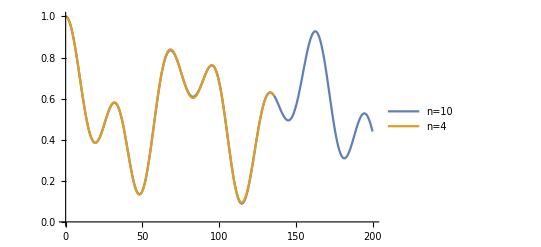

```mathematica
p2=Import["POP_2.txt","Table"];
p3=Import["POP_3.txt","Table"];
```

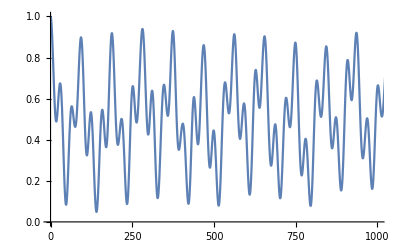

```mathematica
tim[x_,y_:1]:=Table[{(0.002/50)*5.308*1000*n/y,x[[n,2]]},{n,1,Length[x]}];
ListLinePlot[{tim[p2],tim[p3]}[[{2}]],PlotRange->{{0,1000},All},PlotLegends->Automatic]
```